```mathematica
ClearAll;
Clear[mainDataList1];
Clear[mainDataList2];
Clear[mainDataList3];
Clear[mainDataList4];
Clear[mainDataList5];
Clear[mainDataList6];
Clear[data1];
Clear[data2];
Clear[data3];
Clear[data4];
Clear[data5];
Clear[data6];
```

```mathematica
<<IGraphM``
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

```mathematica
data1 = {
	{9,2,2, 4 ,  4,0,0,3,0,3,0,1,0,0},
	{0,2,0, 0 ,  0,0,0,0,0,0,0,0,0,0},
	{0,1,1, 1 ,  1,0,0,0,0,0,0,0,0,0},
	{5,0,0,11,  5,0,0,0,0,3,0,0,0,0},
	{6,0,0,12,18,0,0,0,0,3,0,0,0,0},
	{1,0,0, 0 ,  0,2,3,0,0,0,0,0,0,0},
	{1,0,0, 0 ,  0,0,1,0,0,0,0,0,0,0},
	{1,0,0, 0 ,  0,0,0,0,0,0,0,1,0,0},
	{0,0,0, 0 ,  0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0 ,   0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0 ,   0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0 ,   0,0,0,0,0,0,0,1,0,0},
	{0,0,0,0 ,   0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0 ,   0,0,0,0,0,0,0,0,0,0} 
};
```

```mathematica
Dimensions@data1
```

{14,14}

```mathematica
mainDataList1= {};


yearForData=2015;
For[i=1, i<=14, i++,
For[j=1, j<=14, j++,
AppendTo[mainDataList1,{i,j,yearForData,data1[[i]][[j]]}];
];
];

Length@mainDataList1
```

196

```mathematica
mainDataList1
```

{{1,1,2015,9},{1,2,2015,2},{1,3,2015,2},{1,4,2015,4},{1,5,2015,4},{1,6,2015,0},{1,7,2015,0},{1,8,2015,3},{1,9,2015,0},{1,10,2015,3},{1,11,2015,0},{1,12,2015,1},{1,13,2015,0},{1,14,2015,0},{2,1,2015,0},{2,2,2015,2},{2,3,2015,0},{2,4,2015,0},{2,5,2015,0},{2,6,2015,0},{2,7,2015,0},{2,8,2015,0},{2,9,2015,0},{2,10,2015,0},{2,11,2015,0},{2,12,2015,0},{2,13,2015,0},{2,14,2015,0},{3,1,2015,0},{3,2,2015,1},{3,3,2015,1},{3,4,2015,1},{3,5,2015,1},{3,6,2015,0},{3,7,2015,0},{3,8,2015,0},{3,9,2015,0},{3,10,2015,0},{3,11,2015,0},{3,12,2015,0},{3,13,2015,0},{3,14,2015,0},{4,1,2015,5},{4,2,2015,0},{4,3,2015,0},{4,4,2015,11},{4,5,2015,5},{4,6,2015,0},{4,7,2015,0},{4,8,2015,0},{4,9,2015,0},{4,10,2015,3},{4,11,2015,0},{4,12,2015,0},{4,13,2015,0},{4,14,2015,0},{5,1,2015,6},{5,2,2015,0},{5,3,2015,0},{5,4,2015,12},{5,5,2015,18},{5,6,2015,0},{5,7,2015,0},{5,8,2015,0},{5,9,2015,0},{5,10,2015,3},{5,11,2015,0},{5,12,2015,0},{5,13,2015,0},{5,14,2015,0},{6,1,2015,1},{6,2,2015,0},{6,3,2015,0},{6,4,2015,0},{6,5,2015,0},{6,6,2015,2},{6,7,2015,3},{6,8,2015,0},{6,9,2015,0},{6,10,2015,0},{6,11,2015,0},{6,12,2015,0},{6,13,2015,0},{6,14,2015,0},{7,1,2015,1},{7,2,2015,0},{7,3,2015,0},{7,4,2015,0},{7,5,2015,0},{7,6,2015,0},{7,7,2015,1},{7,8,2015,0},{7,9,2015,0},{7,10,2015,0},{7,11,2015,0},{7,12,2015,0},{7,13,2015,0},{7,14,2015,0},{8,1,2015,1},{8,2,2015,0},{8,3,2015,0},{8,4,2015,0},{8,5,2015,0},{8,6,2015,0},{8,7,2015,0},{8,8,2015,0},{8,9,2015,0},{8,10,2015,0},{8,11,2015,0},{8,12,2015,1},{8,13,2015,0},{8,14,2015,0},{9,1,2015,0},{9,2,2015,0},{9,3,2015,0},{9,4,2015,0},{9,5,2015,0},{9,6,2015,0},{9,7,2015,0},{9,8,2015,0},{9,9,2015,0},{9,10,2015,0},{9,11,2015,0},{9,12,2015,0},{9,13,2015,0},{9,14,2015,0},{10,1,2015,0},{10,2,2015,0},{10,3,2015,0},{10,4,2015,0},{10,5,2015,0},{10,6,2015,0},{10,7,2015,0},{10,8,2015,0},{10,9,2015,0},{10,10,2015,0},{10,11,2015,0},{10,12,2015,0},{10,13,2015,0},{10,14,2015,0},{11,1,2015,0},{11,2,2015,0},{11,3,2015,0},{11,4,2015,0},{11,5,2015,0},{11,6,2015,0},{11,7,2015,0},{11,8,2015,0},{11,9,2015,0},{11,10,2015,0},{11,11,2015,0},{11,12,2015,0},{11,13,2015,0},{11,14,2015,0},{12,1,2015,0},{12,2,2015,0},{12,3,2015,0},{12,4,2015,0},{12,5,2015,0},{12,6,2015,0},{12,7,2015,0},{12,8,2015,0},{12,9,2015,0},{12,10,2015,0},{12,11,2015,0},{12,12,2015,1},{12,13,2015,0},{12,14,2015,0},{13,1,2015,0},{13,2,2015,0},{13,3,2015,0},{13,4,2015,0},{13,5,2015,0},{13,6,2015,0},{13,7,2015,0},{13,8,2015,0},{13,9,2015,0},{13,10,2015,0},{13,11,2015,0},{13,12,2015,0},{13,13,2015,0},{13,14,2015,0},{14,1,2015,0},{14,2,2015,0},{14,3,2015,0},{14,4,2015,0},{14,5,2015,0},{14,6,2015,0},{14,7,2015,0},{14,8,2015,0},{14,9,2015,0},{14,10,2015,0},{14,11,2015,0},{14,12,2015,0},{14,13,2015,0},{14,14,2015,0}}

```mathematica
data2 = {

	{13,4,2,  4 ,   5,  0,  0,  4, 0, 3,   0,  2,    0,   0},
	{  1,3,0,  0 ,   0,  0,  0,  0, 0, 0,   0,   0,   0,   0},
	{  0,1,2,  3 ,   2,  0,  0,  0, 0, 0,   0,   0,   0,   0},
	{  6,0,0,18,  10,  0,  0,  0, 0, 4,   0,  0,   0,   0},
	{11,3,1,32,  51,  0,  0, 0, 0, 5,  0,    0,   0,   0},
	{  1,0,0,  0 ,   0,  4,  3,  0, 0, 0,  0,    0,   0,   0},
	{  1,0,0,  0 ,   0,  2,  1,  0, 0, 0,  0,    0,   0,   0},
	{  3,0,0,  0 ,   0,  0,  0,  1, 0, 0,  0,    2,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0, 0,  0,    0,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0, 0,  0,    0,   0,   0},
	{  2,1,0,12 , 19, 0,  0,  0, 0, 0, 11,   0,   0,   0},
	{  1,0,0,  0 ,   0,  0,  0,  1, 0, 0,  0,    2,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0, 0,  0,    0,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0, 0,  0,    0,   0,   0} 
};
```

```mathematica
Dimensions@data2
mainDataList2 = mainDataList1;

yearForData=2016;
For[i=1, i<=14, i++,
For[j=1, j<=14, j++,
AppendTo[mainDataList2,{i,j,yearForData,data2[[i]][[j]]}];
];
];

Dimensions@mainDataList2
mainDataList2
```

{14,14}

{392,4}

{{1,1,2015,9},{1,2,2015,2},{1,3,2015,2},{1,4,2015,4},{1,5,2015,4},{1,6,2015,0},{1,7,2015,0},{1,8,2015,3},{1,9,2015,0},{1,10,2015,3},{1,11,2015,0},{1,12,2015,1},{1,13,2015,0},{1,14,2015,0},{2,1,2015,0},{2,2,2015,2},{2,3,2015,0},{2,4,2015,0},{2,5,2015,0},{2,6,2015,0},{2,7,2015,0},{2,8,2015,0},{2,9,2015,0},{2,10,2015,0},{2,11,2015,0},{2,12,2015,0},{2,13,2015,0},{2,14,2015,0},{3,1,2015,0},{3,2,2015,1},{3,3,2015,1},{3,4,2015,1},{3,5,2015,1},{3,6,2015,0},{3,7,2015,0},{3,8,2015,0},{3,9,2015,0},{3,10,2015,0},{3,11,2015,0},{3,12,2015,0},{3,13,2015,0},{3,14,2015,0},{4,1,2015,5},{4,2,2015,0},{4,3,2015,0},{4,4,2015,11},{4,5,2015,5},{4,6,2015,0},{4,7,2015,0},{4,8,2015,0},{4,9,2015,0},{4,10,2015,3},{4,11,2015,0},{4,12,2015,0},{4,13,2015,0},{4,14,2015,0},{5,1,2015,6},{5,2,2015,0},{5,3,2015,0},{5,4,2015,12},{5,5,2015,18},{5,6,2015,0},{5,7,2015,0},{5,8,2015,0},{5,9,2015,0},{5,10,2015,3},{5,11,2015,0},{5,12,2015,0},{5,13,2015,0},{5,14,2015,0},{6,1,2015,1},{6,2,2015,0},{6,3,2015,0},{6,4,2015,0},{6,5,2015,0},{6,6,2015,2},{6,7,2015,3},{6,8,2015,0},{6,9,2015,0},{6,10,2015,0},{6,11,2015,0},{6,12,2015,0},{6,13,2015,0},{6,14,2015,0},{7,1,2015,1},{7,2,2015,0},{7,3,2015,0},{7,4,2015,0},{7,5,2015,0},{7,6,2015,0},{7,7,2015,1},{7,8,2015,0},{7,9,2015,0},{7,10,2015,0},{7,11,2015,0},{7,12,2015,0},{7,13,2015,0},{7,14,2015,0},{8,1,2015,1},{8,2,2015,0},{8,3,2015,0},{8,4,2015,0},{8,5,2015,0},{8,6,2015,0},{8,7,2015,0},{8,8,2015,0},{8,9,2015,0},{8,10,2015,0},{8,11,2015,0},{8,12,2015,1},{8,13,2015,0},{8,14,2015,0},{9,1,2015,0},{9,2,2015,0},{9,3,2015,0},{9,4,2015,0},{9,5,2015,0},{9,6,2015,0},{9,7,2015,0},{9,8,2015,0},{9,9,2015,0},{9,10,2015,0},{9,11,2015,0},{9,12,2015,0},{9,13,2015,0},{9,14,2015,0},{10,1,2015,0},{10,2,2015,0},{10,3,2015,0},{10,4,2015,0},{10,5,2015,0},{10,6,2015,0},{10,7,2015,0},{10,8,2015,0},{10,9,2015,0},{10,10,2015,0},{10,11,2015,0},{10,12,2015,0},{10,13,2015,0},{10,14,2015,0},{11,1,2015,0},{11,2,2015,0},{11,3,2015,0},{11,4,2015,0},{11,5,2015,0},{11,6,2015,0},{11,7,2015,0},{11,8,2015,0},{11,9,2015,0},{11,10,2015,0},{11,11,2015,0},{11,12,2015,0},{11,13,2015,0},{11,14,2015,0},{12,1,2015,0},{12,2,2015,0},{12,3,2015,0},{12,4,2015,0},{12,5,2015,0},{12,6,2015,0},{12,7,2015,0},{12,8,2015,0},{12,9,2015,0},{12,10,2015,0},{12,11,2015,0},{12,12,2015,1},{12,13,2015,0},{12,14,2015,0},{13,1,2015,0},{13,2,2015,0},{13,3,2015,0},{13,4,2015,0},{13,5,2015,0},{13,6,2015,0},{13,7,2015,0},{13,8,2015,0},{13,9,2015,0},{13,10,2015,0},{13,11,2015,0},{13,12,2015,0},{13,13,2015,0},{13,14,2015,0},{14,1,2015,0},{14,2,2015,0},{14,3,2015,0},{14,4,2015,0},{14,5,2015,0},{14,6,2015,0},{14,7,2015,0},{14,8,2015,0},{14,9,2015,0},{14,10,2015,0},{14,11,2015,0},{14,12,2015,0},{14,13,2015,0},{14,14,2015,0},{1,1,2016,13},{1,2,2016,4},{1,3,2016,2},{1,4,2016,4},{1,5,2016,5},{1,6,2016,0},{1,7,2016,0},{1,8,2016,4},{1,9,2016,0},{1,10,2016,3},{1,11,2016,0},{1,12,2016,2},{1,13,2016,0},{1,14,2016,0},{2,1,2016,1},{2,2,2016,3},{2,3,2016,0},{2,4,2016,0},{2,5,2016,0},{2,6,2016,0},{2,7,2016,0},{2,8,2016,0},{2,9,2016,0},{2,10,2016,0},{2,11,2016,0},{2,12,2016,0},{2,13,2016,0},{2,14,2016,0},{3,1,2016,0},{3,2,2016,1},{3,3,2016,2},{3,4,2016,3},{3,5,2016,2},{3,6,2016,0},{3,7,2016,0},{3,8,2016,0},{3,9,2016,0},{3,10,2016,0},{3,11,2016,0},{3,12,2016,0},{3,13,2016,0},{3,14,2016,0},{4,1,2016,6},{4,2,2016,0},{4,3,2016,0},{4,4,2016,18},{4,5,2016,10},{4,6,2016,0},{4,7,2016,0},{4,8,2016,0},{4,9,2016,0},{4,10,2016,4},{4,11,2016,0},{4,12,2016,0},{4,13,2016,0},{4,14,2016,0},{5,1,2016,11},{5,2,2016,3},{5,3,2016,1},{5,4,2016,32},{5,5,2016,51},{5,6,2016,0},{5,7,2016,0},{5,8,2016,0},{5,9,2016,0},{5,10,2016,5},{5,11,2016,0},{5,12,2016,0},{5,13,2016,0},{5,14,2016,0},{6,1,2016,1},{6,2,2016,0},{6,3,2016,0},{6,4,2016,0},{6,5,2016,0},{6,6,2016,4},{6,7,2016,3},{6,8,2016,0},{6,9,2016,0},{6,10,2016,0},{6,11,2016,0},{6,12,2016,0},{6,13,2016,0},{6,14,2016,0},{7,1,2016,1},{7,2,2016,0},{7,3,2016,0},{7,4,2016,0},{7,5,2016,0},{7,6,2016,2},{7,7,2016,1},{7,8,2016,0},{7,9,2016,0},{7,10,2016,0},{7,11,2016,0},{7,12,2016,0},{7,13,2016,0},{7,14,2016,0},{8,1,2016,3},{8,2,2016,0},{8,3,2016,0},{8,4,2016,0},{8,5,2016,0},{8,6,2016,0},{8,7,2016,0},{8,8,2016,1},{8,9,2016,0},{8,10,2016,0},{8,11,2016,0},{8,12,2016,2},{8,13,2016,0},{8,14,2016,0},{9,1,2016,0},{9,2,2016,0},{9,3,2016,0},{9,4,2016,0},{9,5,2016,0},{9,6,2016,0},{9,7,2016,0},{9,8,2016,0},{9,9,2016,0},{9,10,2016,0},{9,11,2016,0},{9,12,2016,0},{9,13,2016,0},{9,14,2016,0},{10,1,2016,0},{10,2,2016,0},{10,3,2016,0},{10,4,2016,0},{10,5,2016,0},{10,6,2016,0},{10,7,2016,0},{10,8,2016,0},{10,9,2016,0},{10,10,2016,0},{10,11,2016,0},{10,12,2016,0},{10,13,2016,0},{10,14,2016,0},{11,1,2016,2},{11,2,2016,1},{11,3,2016,0},{11,4,2016,12},{11,5,2016,19},{11,6,2016,0},{11,7,2016,0},{11,8,2016,0},{11,9,2016,0},{11,10,2016,0},{11,11,2016,11},{11,12,2016,0},{11,13,2016,0},{11,14,2016,0},{12,1,2016,1},{12,2,2016,0},{12,3,2016,0},{12,4,2016,0},{12,5,2016,0},{12,6,2016,0},{12,7,2016,0},{12,8,2016,1},{12,9,2016,0},{12,10,2016,0},{12,11,2016,0},{12,12,2016,2},{12,13,2016,0},{12,14,2016,0},{13,1,2016,0},{13,2,2016,0},{13,3,2016,0},{13,4,2016,0},{13,5,2016,0},{13,6,2016,0},{13,7,2016,0},{13,8,2016,0},{13,9,2016,0},{13,10,2016,0},{13,11,2016,0},{13,12,2016,0},{13,13,2016,0},{13,14,2016,0},{14,1,2016,0},{14,2,2016,0},{14,3,2016,0},{14,4,2016,0},{14,5,2016,0},{14,6,2016,0},{14,7,2016,0},{14,8,2016,0},{14,9,2016,0},{14,10,2016,0},{14,11,2016,0},{14,12,2016,0},{14,13,2016,0},{14,14,2016,0}}

```mathematica
data3 = {

	{14,4,2,  4 ,   5,  0,  0,  5, 0, 3,   0,   4,    0,   0},
	{  1,3,0,  0 ,   0,  0,  0,  0, 0, 0,   0,   0,   0,   0},
	{  0,2,3,  4 ,   3,  0,  0,  0, 0, 0,   0,   0,   0,   0},
	{  7,0,0,23,  13,  0,  0,  0, 0, 5,   2,   0,   0,   0},
	{12,4,1,32,  72,  0,  0, 0, 0,  6,  12,  0,   0,   0},
	{  1,0,0,  0 ,   0,  5,  4,  0, 0,  0,   0,    0,   0,   0},
	{  1,0,0,  0 ,   0,  3,  2,  0, 0,  0,   0,    0,   0,   0},
	{  4,0,0,  0 ,   0,  0,  0,  2, 0,  0,   0,    3,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0,  0,   0,    0,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0,  0,   0,    0,   0,   0},
	{  3,2,0,23 , 39, 0,  0,  0, 0,  3,  11,   0,   0,   0},
	{  2,0,0,  0 ,   0,  0,  0,  2, 0,  0,   0,    5,   0,   0},
	{  1,0,0,  7 ,  14,  0,  0,  0, 0, 1,   7,    0,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0, 0,    0,    0,   0,   0} 
};
```

```mathematica
Dimensions@data3
mainDataList3 = mainDataList2;

yearForData=2017;
For[i=1, i<=14, i++,
For[j=1, j<=14, j++,
AppendTo[mainDataList3,{i,j,yearForData,data3[[i]][[j]]}];
];
];

Dimensions@mainDataList3
mainDataList3
```

{14,14}

{588,4}

{{1,1,2015,9},{1,2,2015,2},{1,3,2015,2},{1,4,2015,4},{1,5,2015,4},{1,6,2015,0},{1,7,2015,0},{1,8,2015,3},{1,9,2015,0},{1,10,2015,3},{1,11,2015,0},{1,12,2015,1},{1,13,2015,0},{1,14,2015,0},{2,1,2015,0},{2,2,2015,2},{2,3,2015,0},{2,4,2015,0},{2,5,2015,0},{2,6,2015,0},{2,7,2015,0},{2,8,2015,0},{2,9,2015,0},{2,10,2015,0},{2,11,2015,0},{2,12,2015,0},{2,13,2015,0},{2,14,2015,0},{3,1,2015,0},{3,2,2015,1},{3,3,2015,1},{3,4,2015,1},{3,5,2015,1},{3,6,2015,0},{3,7,2015,0},{3,8,2015,0},{3,9,2015,0},{3,10,2015,0},{3,11,2015,0},{3,12,2015,0},{3,13,2015,0},{3,14,2015,0},{4,1,2015,5},{4,2,2015,0},{4,3,2015,0},{4,4,2015,11},{4,5,2015,5},{4,6,2015,0},{4,7,2015,0},{4,8,2015,0},{4,9,2015,0},{4,10,2015,3},{4,11,2015,0},{4,12,2015,0},{4,13,2015,0},{4,14,2015,0},{5,1,2015,6},{5,2,2015,0},{5,3,2015,0},{5,4,2015,12},{5,5,2015,18},{5,6,2015,0},{5,7,2015,0},{5,8,2015,0},{5,9,2015,0},{5,10,2015,3},{5,11,2015,0},{5,12,2015,0},{5,13,2015,0},{5,14,2015,0},{6,1,2015,1},{6,2,2015,0},{6,3,2015,0},{6,4,2015,0},{6,5,2015,0},{6,6,2015,2},{6,7,2015,3},{6,8,2015,0},{6,9,2015,0},{6,10,2015,0},{6,11,2015,0},{6,12,2015,0},{6,13,2015,0},{6,14,2015,0},{7,1,2015,1},{7,2,2015,0},{7,3,2015,0},{7,4,2015,0},{7,5,2015,0},{7,6,2015,0},{7,7,2015,1},{7,8,2015,0},{7,9,2015,0},{7,10,2015,0},{7,11,2015,0},{7,12,2015,0},{7,13,2015,0},{7,14,2015,0},{8,1,2015,1},{8,2,2015,0},{8,3,2015,0},{8,4,2015,0},{8,5,2015,0},{8,6,2015,0},{8,7,2015,0},{8,8,2015,0},{8,9,2015,0},{8,10,2015,0},{8,11,2015,0},{8,12,2015,1},{8,13,2015,0},{8,14,2015,0},{9,1,2015,0},{9,2,2015,0},{9,3,2015,0},{9,4,2015,0},{9,5,2015,0},{9,6,2015,0},{9,7,2015,0},{9,8,2015,0},{9,9,2015,0},{9,10,2015,0},{9,11,2015,0},{9,12,2015,0},{9,13,2015,0},{9,14,2015,0},{10,1,2015,0},{10,2,2015,0},{10,3,2015,0},{10,4,2015,0},{10,5,2015,0},{10,6,2015,0},{10,7,2015,0},{10,8,2015,0},{10,9,2015,0},{10,10,2015,0},{10,11,2015,0},{10,12,2015,0},{10,13,2015,0},{10,14,2015,0},{11,1,2015,0},{11,2,2015,0},{11,3,2015,0},{11,4,2015,0},{11,5,2015,0},{11,6,2015,0},{11,7,2015,0},{11,8,2015,0},{11,9,2015,0},{11,10,2015,0},{11,11,2015,0},{11,12,2015,0},{11,13,2015,0},{11,14,2015,0},{12,1,2015,0},{12,2,2015,0},{12,3,2015,0},{12,4,2015,0},{12,5,2015,0},{12,6,2015,0},{12,7,2015,0},{12,8,2015,0},{12,9,2015,0},{12,10,2015,0},{12,11,2015,0},{12,12,2015,1},{12,13,2015,0},{12,14,2015,0},{13,1,2015,0},{13,2,2015,0},{13,3,2015,0},{13,4,2015,0},{13,5,2015,0},{13,6,2015,0},{13,7,2015,0},{13,8,2015,0},{13,9,2015,0},{13,10,2015,0},{13,11,2015,0},{13,12,2015,0},{13,13,2015,0},{13,14,2015,0},{14,1,2015,0},{14,2,2015,0},{14,3,2015,0},{14,4,2015,0},{14,5,2015,0},{14,6,2015,0},{14,7,2015,0},{14,8,2015,0},{14,9,2015,0},{14,10,2015,0},{14,11,2015,0},{14,12,2015,0},{14,13,2015,0},{14,14,2015,0},{1,1,2016,13},{1,2,2016,4},{1,3,2016,2},{1,4,2016,4},{1,5,2016,5},{1,6,2016,0},{1,7,2016,0},{1,8,2016,4},{1,9,2016,0},{1,10,2016,3},{1,11,2016,0},{1,12,2016,2},{1,13,2016,0},{1,14,2016,0},{2,1,2016,1},{2,2,2016,3},{2,3,2016,0},{2,4,2016,0},{2,5,2016,0},{2,6,2016,0},{2,7,2016,0},{2,8,2016,0},{2,9,2016,0},{2,10,2016,0},{2,11,2016,0},{2,12,2016,0},{2,13,2016,0},{2,14,2016,0},{3,1,2016,0},{3,2,2016,1},{3,3,2016,2},{3,4,2016,3},{3,5,2016,2},{3,6,2016,0},{3,7,2016,0},{3,8,2016,0},{3,9,2016,0},{3,10,2016,0},{3,11,2016,0},{3,12,2016,0},{3,13,2016,0},{3,14,2016,0},{4,1,2016,6},{4,2,2016,0},{4,3,2016,0},{4,4,2016,18},{4,5,2016,10},{4,6,2016,0},{4,7,2016,0},{4,8,2016,0},{4,9,2016,0},{4,10,2016,4},{4,11,2016,0},{4,12,2016,0},{4,13,2016,0},{4,14,2016,0},{5,1,2016,11},{5,2,2016,3},{5,3,2016,1},{5,4,2016,32},{5,5,2016,51},{5,6,2016,0},{5,7,2016,0},{5,8,2016,0},{5,9,2016,0},{5,10,2016,5},{5,11,2016,0},{5,12,2016,0},{5,13,2016,0},{5,14,2016,0},{6,1,2016,1},{6,2,2016,0},{6,3,2016,0},{6,4,2016,0},{6,5,2016,0},{6,6,2016,4},{6,7,2016,3},{6,8,2016,0},{6,9,2016,0},{6,10,2016,0},{6,11,2016,0},{6,12,2016,0},{6,13,2016,0},{6,14,2016,0},{7,1,2016,1},{7,2,2016,0},{7,3,2016,0},{7,4,2016,0},{7,5,2016,0},{7,6,2016,2},{7,7,2016,1},{7,8,2016,0},{7,9,2016,0},{7,10,2016,0},{7,11,2016,0},{7,12,2016,0},{7,13,2016,0},{7,14,2016,0},{8,1,2016,3},{8,2,2016,0},{8,3,2016,0},{8,4,2016,0},{8,5,2016,0},{8,6,2016,0},{8,7,2016,0},{8,8,2016,1},{8,9,2016,0},{8,10,2016,0},{8,11,2016,0},{8,12,2016,2},{8,13,2016,0},{8,14,2016,0},{9,1,2016,0},{9,2,2016,0},{9,3,2016,0},{9,4,2016,0},{9,5,2016,0},{9,6,2016,0},{9,7,2016,0},{9,8,2016,0},{9,9,2016,0},{9,10,2016,0},{9,11,2016,0},{9,12,2016,0},{9,13,2016,0},{9,14,2016,0},{10,1,2016,0},{10,2,2016,0},{10,3,2016,0},{10,4,2016,0},{10,5,2016,0},{10,6,2016,0},{10,7,2016,0},{10,8,2016,0},{10,9,2016,0},{10,10,2016,0},{10,11,2016,0},{10,12,2016,0},{10,13,2016,0},{10,14,2016,0},{11,1,2016,2},{11,2,2016,1},{11,3,2016,0},{11,4,2016,12},{11,5,2016,19},{11,6,2016,0},{11,7,2016,0},{11,8,2016,0},{11,9,2016,0},{11,10,2016,0},{11,11,2016,11},{11,12,2016,0},{11,13,2016,0},{11,14,2016,0},{12,1,2016,1},{12,2,2016,0},{12,3,2016,0},{12,4,2016,0},{12,5,2016,0},{12,6,2016,0},{12,7,2016,0},{12,8,2016,1},{12,9,2016,0},{12,10,2016,0},{12,11,2016,0},{12,12,2016,2},{12,13,2016,0},{12,14,2016,0},{13,1,2016,0},{13,2,2016,0},{13,3,2016,0},{13,4,2016,0},{13,5,2016,0},{13,6,2016,0},{13,7,2016,0},{13,8,2016,0},{13,9,2016,0},{13,10,2016,0},{13,11,2016,0},{13,12,2016,0},{13,13,2016,0},{13,14,2016,0},{14,1,2016,0},{14,2,2016,0},{14,3,2016,0},{14,4,2016,0},{14,5,2016,0},{14,6,2016,0},{14,7,2016,0},{14,8,2016,0},{14,9,2016,0},{14,10,2016,0},{14,11,2016,0},{14,12,2016,0},{14,13,2016,0},{14,14,2016,0},{1,1,2017,14},{1,2,2017,4},{1,3,2017,2},{1,4,2017,4},{1,5,2017,5},{1,6,2017,0},{1,7,2017,0},{1,8,2017,5},{1,9,2017,0},{1,10,2017,3},{1,11,2017,0},{1,12,2017,4},{1,13,2017,0},{1,14,2017,0},{2,1,2017,1},{2,2,2017,3},{2,3,2017,0},{2,4,2017,0},{2,5,2017,0},{2,6,2017,0},{2,7,2017,0},{2,8,2017,0},{2,9,2017,0},{2,10,2017,0},{2,11,2017,0},{2,12,2017,0},{2,13,2017,0},{2,14,2017,0},{3,1,2017,0},{3,2,2017,2},{3,3,2017,3},{3,4,2017,4},{3,5,2017,3},{3,6,2017,0},{3,7,2017,0},{3,8,2017,0},{3,9,2017,0},{3,10,2017,0},{3,11,2017,0},{3,12,2017,0},{3,13,2017,0},{3,14,2017,0},{4,1,2017,7},{4,2,2017,0},{4,3,2017,0},{4,4,2017,23},{4,5,2017,13},{4,6,2017,0},{4,7,2017,0},{4,8,2017,0},{4,9,2017,0},{4,10,2017,5},{4,11,2017,2},{4,12,2017,0},{4,13,2017,0},{4,14,2017,0},{5,1,2017,12},{5,2,2017,4},{5,3,2017,1},{5,4,2017,32},{5,5,2017,72},{5,6,2017,0},{5,7,2017,0},{5,8,2017,0},{5,9,2017,0},{5,10,2017,6},{5,11,2017,12},{5,12,2017,0},{5,13,2017,0},{5,14,2017,0},{6,1,2017,1},{6,2,2017,0},{6,3,2017,0},{6,4,2017,0},{6,5,2017,0},{6,6,2017,5},{6,7,2017,4},{6,8,2017,0},{6,9,2017,0},{6,10,2017,0},{6,11,2017,0},{6,12,2017,0},{6,13,2017,0},{6,14,2017,0},{7,1,2017,1},{7,2,2017,0},{7,3,2017,0},{7,4,2017,0},{7,5,2017,0},{7,6,2017,3},{7,7,2017,2},{7,8,2017,0},{7,9,2017,0},{7,10,2017,0},{7,11,2017,0},{7,12,2017,0},{7,13,2017,0},{7,14,2017,0},{8,1,2017,4},{8,2,2017,0},{8,3,2017,0},{8,4,2017,0},{8,5,2017,0},{8,6,2017,0},{8,7,2017,0},{8,8,2017,2},{8,9,2017,0},{8,10,2017,0},{8,11,2017,0},{8,12,2017,3},{8,13,2017,0},{8,14,2017,0},{9,1,2017,0},{9,2,2017,0},{9,3,2017,0},{9,4,2017,0},{9,5,2017,0},{9,6,2017,0},{9,7,2017,0},{9,8,2017,0},{9,9,2017,0},{9,10,2017,0},{9,11,2017,0},{9,12,2017,0},{9,13,2017,0},{9,14,2017,0},{10,1,2017,0},{10,2,2017,0},{10,3,2017,0},{10,4,2017,0},{10,5,2017,0},{10,6,2017,0},{10,7,2017,0},{10,8,2017,0},{10,9,2017,0},{10,10,2017,0},{10,11,2017,0},{10,12,2017,0},{10,13,2017,0},{10,14,2017,0},{11,1,2017,3},{11,2,2017,2},{11,3,2017,0},{11,4,2017,23},{11,5,2017,39},{11,6,2017,0},{11,7,2017,0},{11,8,2017,0},{11,9,2017,0},{11,10,2017,3},{11,11,2017,11},{11,12,2017,0},{11,13,2017,0},{11,14,2017,0},{12,1,2017,2},{12,2,2017,0},{12,3,2017,0},{12,4,2017,0},{12,5,2017,0},{12,6,2017,0},{12,7,2017,0},{12,8,2017,2},{12,9,2017,0},{12,10,2017,0},{12,11,2017,0},{12,12,2017,5},{12,13,2017,0},{12,14,2017,0},{13,1,2017,1},{13,2,2017,0},{13,3,2017,0},{13,4,2017,7},{13,5,2017,14},{13,6,2017,0},{13,7,2017,0},{13,8,2017,0},{13,9,2017,0},{13,10,2017,1},{13,11,2017,7},{13,12,2017,0},{13,13,2017,0},{13,14,2017,0},{14,1,2017,0},{14,2,2017,0},{14,3,2017,0},{14,4,2017,0},{14,5,2017,0},{14,6,2017,0},{14,7,2017,0},{14,8,2017,0},{14,9,2017,0},{14,10,2017,0},{14,11,2017,0},{14,12,2017,0},{14,13,2017,0},{14,14,2017,0}}

```mathematica
data4={
	{  16,5,2,  4 ,   6,  0,  0,  5, 0, 3,   0,   5,    0,   0},
	{  2,4,0,  1 ,   1,  0,  0,  0, 0, 0,   0,   1,   0,    0},
	{  1,3,3,  4 ,   3,  0,  0,  0, 0, 0,   0,   1,   0,    0},
	{  9,0,0,30,  20,  0,  0,  0, 0, 6,   8,   0,   3,    0},
	{14,4,1,57, 103,  0,  0, 0, 0, 7,  37,  0,  18,  0},
	{  1,0,0,  0 ,   0,  5,  4,  0, 0,  0,   0,    0,   0,   0},
	{  1,0,0,  0 ,   0,  3,  2,  0, 0,  0,   0,    0,   0,   0},
	{  5,0,0,  0 ,   0,  0,  0,  2, 0,  0,   0,    3,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0,  0,   0,    0,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0,  0,   0,    0,   0,   0},
	{  5,2,0,35 , 62, 0,  0,  0, 0,  4,  34,   0,  17,  0},
	{  4,1,0,  0 ,   0,  1,  0,  2, 0,  0,   0,    6,   0,   0},
	{  1,0,0, 17 , 36,  0,  0, 0, 0,  1,  29,   0,  17,  0},
	{  0,0,0,  0 ,   0,   0,  0,  0, 0,  0,    0,    0,   0,   0} 
};
```

```mathematica
Dimensions@data4
mainDataList4 = mainDataList3;

yearForData=2018;
For[i=1, i<=14, i++,
For[j=1, j<=14, j++,
AppendTo[mainDataList4,{i,j,yearForData,data4[[i]][[j]]}];
];
];

Dimensions@mainDataList4
mainDataList4
```

{14,14}

{784,4}

{{1,1,2015,9},{1,2,2015,2},{1,3,2015,2},{1,4,2015,4},{1,5,2015,4},{1,6,2015,0},{1,7,2015,0},{1,8,2015,3},{1,9,2015,0},{1,10,2015,3},{1,11,2015,0},{1,12,2015,1},{1,13,2015,0},{1,14,2015,0},{2,1,2015,0},{2,2,2015,2},{2,3,2015,0},{2,4,2015,0},{2,5,2015,0},{2,6,2015,0},{2,7,2015,0},{2,8,2015,0},{2,9,2015,0},{2,10,2015,0},{2,11,2015,0},{2,12,2015,0},{2,13,2015,0},{2,14,2015,0},{3,1,2015,0},{3,2,2015,1},{3,3,2015,1},{3,4,2015,1},{3,5,2015,1},{3,6,2015,0},{3,7,2015,0},{3,8,2015,0},{3,9,2015,0},{3,10,2015,0},{3,11,2015,0},{3,12,2015,0},{3,13,2015,0},{3,14,2015,0},{4,1,2015,5},{4,2,2015,0},{4,3,2015,0},{4,4,2015,11},{4,5,2015,5},{4,6,2015,0},{4,7,2015,0},{4,8,2015,0},{4,9,2015,0},{4,10,2015,3},{4,11,2015,0},{4,12,2015,0},{4,13,2015,0},{4,14,2015,0},{5,1,2015,6},{5,2,2015,0},{5,3,2015,0},{5,4,2015,12},{5,5,2015,18},{5,6,2015,0},{5,7,2015,0},{5,8,2015,0},{5,9,2015,0},{5,10,2015,3},{5,11,2015,0},{5,12,2015,0},{5,13,2015,0},{5,14,2015,0},{6,1,2015,1},{6,2,2015,0},{6,3,2015,0},{6,4,2015,0},{6,5,2015,0},{6,6,2015,2},{6,7,2015,3},{6,8,2015,0},{6,9,2015,0},{6,10,2015,0},{6,11,2015,0},{6,12,2015,0},{6,13,2015,0},{6,14,2015,0},{7,1,2015,1},{7,2,2015,0},{7,3,2015,0},{7,4,2015,0},{7,5,2015,0},{7,6,2015,0},{7,7,2015,1},{7,8,2015,0},{7,9,2015,0},{7,10,2015,0},{7,11,2015,0},{7,12,2015,0},{7,13,2015,0},{7,14,2015,0},{8,1,2015,1},{8,2,2015,0},{8,3,2015,0},{8,4,2015,0},{8,5,2015,0},{8,6,2015,0},{8,7,2015,0},{8,8,2015,0},{8,9,2015,0},{8,10,2015,0},{8,11,2015,0},{8,12,2015,1},{8,13,2015,0},{8,14,2015,0},{9,1,2015,0},{9,2,2015,0},{9,3,2015,0},{9,4,2015,0},{9,5,2015,0},{9,6,2015,0},{9,7,2015,0},{9,8,2015,0},{9,9,2015,0},{9,10,2015,0},{9,11,2015,0},{9,12,2015,0},{9,13,2015,0},{9,14,2015,0},{10,1,2015,0},{10,2,2015,0},{10,3,2015,0},{10,4,2015,0},{10,5,2015,0},{10,6,2015,0},{10,7,2015,0},{10,8,2015,0},{10,9,2015,0},{10,10,2015,0},{10,11,2015,0},{10,12,2015,0},{10,13,2015,0},{10,14,2015,0},{11,1,2015,0},{11,2,2015,0},{11,3,2015,0},{11,4,2015,0},{11,5,2015,0},{11,6,2015,0},{11,7,2015,0},{11,8,2015,0},{11,9,2015,0},{11,10,2015,0},{11,11,2015,0},{11,12,2015,0},{11,13,2015,0},{11,14,2015,0},{12,1,2015,0},{12,2,2015,0},{12,3,2015,0},{12,4,2015,0},{12,5,2015,0},{12,6,2015,0},{12,7,2015,0},{12,8,2015,0},{12,9,2015,0},{12,10,2015,0},{12,11,2015,0},{12,12,2015,1},{12,13,2015,0},{12,14,2015,0},{13,1,2015,0},{13,2,2015,0},{13,3,2015,0},{13,4,2015,0},{13,5,2015,0},{13,6,2015,0},{13,7,2015,0},{13,8,2015,0},{13,9,2015,0},{13,10,2015,0},{13,11,2015,0},{13,12,2015,0},{13,13,2015,0},{13,14,2015,0},{14,1,2015,0},{14,2,2015,0},{14,3,2015,0},{14,4,2015,0},{14,5,2015,0},{14,6,2015,0},{14,7,2015,0},{14,8,2015,0},{14,9,2015,0},{14,10,2015,0},{14,11,2015,0},{14,12,2015,0},{14,13,2015,0},{14,14,2015,0},{1,1,2016,13},{1,2,2016,4},{1,3,2016,2},{1,4,2016,4},{1,5,2016,5},{1,6,2016,0},{1,7,2016,0},{1,8,2016,4},{1,9,2016,0},{1,10,2016,3},{1,11,2016,0},{1,12,2016,2},{1,13,2016,0},{1,14,2016,0},{2,1,2016,1},{2,2,2016,3},{2,3,2016,0},{2,4,2016,0},{2,5,2016,0},{2,6,2016,0},{2,7,2016,0},{2,8,2016,0},{2,9,2016,0},{2,10,2016,0},{2,11,2016,0},{2,12,2016,0},{2,13,2016,0},{2,14,2016,0},{3,1,2016,0},{3,2,2016,1},{3,3,2016,2},{3,4,2016,3},{3,5,2016,2},{3,6,2016,0},{3,7,2016,0},{3,8,2016,0},{3,9,2016,0},{3,10,2016,0},{3,11,2016,0},{3,12,2016,0},{3,13,2016,0},{3,14,2016,0},{4,1,2016,6},{4,2,2016,0},{4,3,2016,0},{4,4,2016,18},{4,5,2016,10},{4,6,2016,0},{4,7,2016,0},{4,8,2016,0},{4,9,2016,0},{4,10,2016,4},{4,11,2016,0},{4,12,2016,0},{4,13,2016,0},{4,14,2016,0},{5,1,2016,11},{5,2,2016,3},{5,3,2016,1},{5,4,2016,32},{5,5,2016,51},{5,6,2016,0},{5,7,2016,0},{5,8,2016,0},{5,9,2016,0},{5,10,2016,5},{5,11,2016,0},{5,12,2016,0},{5,13,2016,0},{5,14,2016,0},{6,1,2016,1},{6,2,2016,0},{6,3,2016,0},{6,4,2016,0},{6,5,2016,0},{6,6,2016,4},{6,7,2016,3},{6,8,2016,0},{6,9,2016,0},{6,10,2016,0},{6,11,2016,0},{6,12,2016,0},{6,13,2016,0},{6,14,2016,0},{7,1,2016,1},{7,2,2016,0},{7,3,2016,0},{7,4,2016,0},{7,5,2016,0},{7,6,2016,2},{7,7,2016,1},{7,8,2016,0},{7,9,2016,0},{7,10,2016,0},{7,11,2016,0},{7,12,2016,0},{7,13,2016,0},{7,14,2016,0},{8,1,2016,3},{8,2,2016,0},{8,3,2016,0},{8,4,2016,0},{8,5,2016,0},{8,6,2016,0},{8,7,2016,0},{8,8,2016,1},{8,9,2016,0},{8,10,2016,0},{8,11,2016,0},{8,12,2016,2},{8,13,2016,0},{8,14,2016,0},{9,1,2016,0},{9,2,2016,0},{9,3,2016,0},{9,4,2016,0},{9,5,2016,0},{9,6,2016,0},{9,7,2016,0},{9,8,2016,0},{9,9,2016,0},{9,10,2016,0},{9,11,2016,0},{9,12,2016,0},{9,13,2016,0},{9,14,2016,0},{10,1,2016,0},{10,2,2016,0},{10,3,2016,0},{10,4,2016,0},{10,5,2016,0},{10,6,2016,0},{10,7,2016,0},{10,8,2016,0},{10,9,2016,0},{10,10,2016,0},{10,11,2016,0},{10,12,2016,0},{10,13,2016,0},{10,14,2016,0},{11,1,2016,2},{11,2,2016,1},{11,3,2016,0},{11,4,2016,12},{11,5,2016,19},{11,6,2016,0},{11,7,2016,0},{11,8,2016,0},{11,9,2016,0},{11,10,2016,0},{11,11,2016,11},{11,12,2016,0},{11,13,2016,0},{11,14,2016,0},{12,1,2016,1},{12,2,2016,0},{12,3,2016,0},{12,4,2016,0},{12,5,2016,0},{12,6,2016,0},{12,7,2016,0},{12,8,2016,1},{12,9,2016,0},{12,10,2016,0},{12,11,2016,0},{12,12,2016,2},{12,13,2016,0},{12,14,2016,0},{13,1,2016,0},{13,2,2016,0},{13,3,2016,0},{13,4,2016,0},{13,5,2016,0},{13,6,2016,0},{13,7,2016,0},{13,8,2016,0},{13,9,2016,0},{13,10,2016,0},{13,11,2016,0},{13,12,2016,0},{13,13,2016,0},{13,14,2016,0},{14,1,2016,0},{14,2,2016,0},{14,3,2016,0},{14,4,2016,0},{14,5,2016,0},{14,6,2016,0},{14,7,2016,0},{14,8,2016,0},{14,9,2016,0},{14,10,2016,0},{14,11,2016,0},{14,12,2016,0},{14,13,2016,0},{14,14,2016,0},{1,1,2017,14},{1,2,2017,4},{1,3,2017,2},{1,4,2017,4},{1,5,2017,5},{1,6,2017,0},{1,7,2017,0},{1,8,2017,5},{1,9,2017,0},{1,10,2017,3},{1,11,2017,0},{1,12,2017,4},{1,13,2017,0},{1,14,2017,0},{2,1,2017,1},{2,2,2017,3},{2,3,2017,0},{2,4,2017,0},{2,5,2017,0},{2,6,2017,0},{2,7,2017,0},{2,8,2017,0},{2,9,2017,0},{2,10,2017,0},{2,11,2017,0},{2,12,2017,0},{2,13,2017,0},{2,14,2017,0},{3,1,2017,0},{3,2,2017,2},{3,3,2017,3},{3,4,2017,4},{3,5,2017,3},{3,6,2017,0},{3,7,2017,0},{3,8,2017,0},{3,9,2017,0},{3,10,2017,0},{3,11,2017,0},{3,12,2017,0},{3,13,2017,0},{3,14,2017,0},{4,1,2017,7},{4,2,2017,0},{4,3,2017,0},{4,4,2017,23},{4,5,2017,13},{4,6,2017,0},{4,7,2017,0},{4,8,2017,0},{4,9,2017,0},{4,10,2017,5},{4,11,2017,2},{4,12,2017,0},{4,13,2017,0},{4,14,2017,0},{5,1,2017,12},{5,2,2017,4},{5,3,2017,1},{5,4,2017,32},{5,5,2017,72},{5,6,2017,0},{5,7,2017,0},{5,8,2017,0},{5,9,2017,0},{5,10,2017,6},{5,11,2017,12},{5,12,2017,0},{5,13,2017,0},{5,14,2017,0},{6,1,2017,1},{6,2,2017,0},{6,3,2017,0},{6,4,2017,0},{6,5,2017,0},{6,6,2017,5},{6,7,2017,4},{6,8,2017,0},{6,9,2017,0},{6,10,2017,0},{6,11,2017,0},{6,12,2017,0},{6,13,2017,0},{6,14,2017,0},{7,1,2017,1},{7,2,2017,0},{7,3,2017,0},{7,4,2017,0},{7,5,2017,0},{7,6,2017,3},{7,7,2017,2},{7,8,2017,0},{7,9,2017,0},{7,10,2017,0},{7,11,2017,0},{7,12,2017,0},{7,13,2017,0},{7,14,2017,0},{8,1,2017,4},{8,2,2017,0},{8,3,2017,0},{8,4,2017,0},{8,5,2017,0},{8,6,2017,0},{8,7,2017,0},{8,8,2017,2},{8,9,2017,0},{8,10,2017,0},{8,11,2017,0},{8,12,2017,3},{8,13,2017,0},{8,14,2017,0},{9,1,2017,0},{9,2,2017,0},{9,3,2017,0},{9,4,2017,0},{9,5,2017,0},{9,6,2017,0},{9,7,2017,0},{9,8,2017,0},{9,9,2017,0},{9,10,2017,0},{9,11,2017,0},{9,12,2017,0},{9,13,2017,0},{9,14,2017,0},{10,1,2017,0},{10,2,2017,0},{10,3,2017,0},{10,4,2017,0},{10,5,2017,0},{10,6,2017,0},{10,7,2017,0},{10,8,2017,0},{10,9,2017,0},{10,10,2017,0},{10,11,2017,0},{10,12,2017,0},{10,13,2017,0},{10,14,2017,0},{11,1,2017,3},{11,2,2017,2},{11,3,2017,0},{11,4,2017,23},{11,5,2017,39},{11,6,2017,0},{11,7,2017,0},{11,8,2017,0},{11,9,2017,0},{11,10,2017,3},{11,11,2017,11},{11,12,2017,0},{11,13,2017,0},{11,14,2017,0},{12,1,2017,2},{12,2,2017,0},{12,3,2017,0},{12,4,2017,0},{12,5,2017,0},{12,6,2017,0},{12,7,2017,0},{12,8,2017,2},{12,9,2017,0},{12,10,2017,0},{12,11,2017,0},{12,12,2017,5},{12,13,2017,0},{12,14,2017,0},{13,1,2017,1},{13,2,2017,0},{13,3,2017,0},{13,4,2017,7},{13,5,2017,14},{13,6,2017,0},{13,7,2017,0},{13,8,2017,0},{13,9,2017,0},{13,10,2017,1},{13,11,2017,7},{13,12,2017,0},{13,13,2017,0},{13,14,2017,0},{14,1,2017,0},{14,2,2017,0},{14,3,2017,0},{14,4,2017,0},{14,5,2017,0},{14,6,2017,0},{14,7,2017,0},{14,8,2017,0},{14,9,2017,0},{14,10,2017,0},{14,11,2017,0},{14,12,2017,0},{14,13,2017,0},{14,14,2017,0},{1,1,2018,16},{1,2,2018,5},{1,3,2018,2},{1,4,2018,4},{1,5,2018,6},{1,6,2018,0},{1,7,2018,0},{1,8,2018,5},{1,9,2018,0},{1,10,2018,3},{1,11,2018,0},{1,12,2018,5},{1,13,2018,0},{1,14,2018,0},{2,1,2018,2},{2,2,2018,4},{2,3,2018,0},{2,4,2018,1},{2,5,2018,1},{2,6,2018,0},{2,7,2018,0},{2,8,2018,0},{2,9,2018,0},{2,10,2018,0},{2,11,2018,0},{2,12,2018,1},{2,13,2018,0},{2,14,2018,0},{3,1,2018,1},{3,2,2018,3},{3,3,2018,3},{3,4,2018,4},{3,5,2018,3},{3,6,2018,0},{3,7,2018,0},{3,8,2018,0},{3,9,2018,0},{3,10,2018,0},{3,11,2018,0},{3,12,2018,1},{3,13,2018,0},{3,14,2018,0},{4,1,2018,9},{4,2,2018,0},{4,3,2018,0},{4,4,2018,30},{4,5,2018,20},{4,6,2018,0},{4,7,2018,0},{4,8,2018,0},{4,9,2018,0},{4,10,2018,6},{4,11,2018,8},{4,12,2018,0},{4,13,2018,3},{4,14,2018,0},{5,1,2018,14},{5,2,2018,4},{5,3,2018,1},{5,4,2018,57},{5,5,2018,103},{5,6,2018,0},{5,7,2018,0},{5,8,2018,0},{5,9,2018,0},{5,10,2018,7},{5,11,2018,37},{5,12,2018,0},{5,13,2018,18},{5,14,2018,0},{6,1,2018,1},{6,2,2018,0},{6,3,2018,0},{6,4,2018,0},{6,5,2018,0},{6,6,2018,5},{6,7,2018,4},{6,8,2018,0},{6,9,2018,0},{6,10,2018,0},{6,11,2018,0},{6,12,2018,0},{6,13,2018,0},{6,14,2018,0},{7,1,2018,1},{7,2,2018,0},{7,3,2018,0},{7,4,2018,0},{7,5,2018,0},{7,6,2018,3},{7,7,2018,2},{7,8,2018,0},{7,9,2018,0},{7,10,2018,0},{7,11,2018,0},{7,12,2018,0},{7,13,2018,0},{7,14,2018,0},{8,1,2018,5},{8,2,2018,0},{8,3,2018,0},{8,4,2018,0},{8,5,2018,0},{8,6,2018,0},{8,7,2018,0},{8,8,2018,2},{8,9,2018,0},{8,10,2018,0},{8,11,2018,0},{8,12,2018,3},{8,13,2018,0},{8,14,2018,0},{9,1,2018,0},{9,2,2018,0},{9,3,2018,0},{9,4,2018,0},{9,5,2018,0},{9,6,2018,0},{9,7,2018,0},{9,8,2018,0},{9,9,2018,0},{9,10,2018,0},{9,11,2018,0},{9,12,2018,0},{9,13,2018,0},{9,14,2018,0},{10,1,2018,0},{10,2,2018,0},{10,3,2018,0},{10,4,2018,0},{10,5,2018,0},{10,6,2018,0},{10,7,2018,0},{10,8,2018,0},{10,9,2018,0},{10,10,2018,0},{10,11,2018,0},{10,12,2018,0},{10,13,2018,0},{10,14,2018,0},{11,1,2018,5},{11,2,2018,2},{11,3,2018,0},{11,4,2018,35},{11,5,2018,62},{11,6,2018,0},{11,7,2018,0},{11,8,2018,0},{11,9,2018,0},{11,10,2018,4},{11,11,2018,34},{11,12,2018,0},{11,13,2018,17},{11,14,2018,0},{12,1,2018,4},{12,2,2018,1},{12,3,2018,0},{12,4,2018,0},{12,5,2018,0},{12,6,2018,1},{12,7,2018,0},{12,8,2018,2},{12,9,2018,0},{12,10,2018,0},{12,11,2018,0},{12,12,2018,6},{12,13,2018,0},{12,14,2018,0},{13,1,2018,1},{13,2,2018,0},{13,3,2018,0},{13,4,2018,17},{13,5,2018,36},{13,6,2018,0},{13,7,2018,0},{13,8,2018,0},{13,9,2018,0},{13,10,2018,1},{13,11,2018,29},{13,12,2018,0},{13,13,2018,17},{13,14,2018,0},{14,1,2018,0},{14,2,2018,0},{14,3,2018,0},{14,4,2018,0},{14,5,2018,0},{14,6,2018,0},{14,7,2018,0},{14,8,2018,0},{14,9,2018,0},{14,10,2018,0},{14,11,2018,0},{14,12,2018,0},{14,13,2018,0},{14,14,2018,0}}

```mathematica
data5 ={
	{18,5,2,  4 ,   8,  0,  0,  5, 0, 3,   0,   5,    0,   0},
	{  3,6,0,  2 ,   2,  0,  0,  0, 0, 0,   0,   1,   0,    0},
	{  1,3,3,  4 ,   3,  0,  0,  0, 0, 0,   0,   1,   0,    0},
	{  9,0,0, 36,  25,  0,  0,  0, 0, 6,  12,   1,   6,    0},
	{15,4,1,57, 122,  0,  0, 0, 0, 7,  52,  0,  32,  0},
	{  1,0,0,  0 ,   0,  5,  4,  0, 0,  0,   0,    0,   0,   0},
	{  1,0,0,  0 ,   0,  3,  2,  0, 0,  0,   0,    0,   0,   0},
	{  6,0,0,  0 ,   1,  0,  0,  2, 0,  0,   0,    3,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0,  0,   0,    0,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0,  0,   0,    0,   0,   0},
	{  5,2,0,40 , 76, 0,  0,  0, 0,  4,  46,   0,  28,  0},
	{  5,1,0,  0 ,   1,  1,  0,  2, 0,  0,   0,    6,   0,   0},
	{  1,0,0, 21 , 49,  0,  0, 0, 0,  1,  41,   0,  28,  0},
	{  0,0,0,  0 ,   0,   0,  0,  0, 0,  0,    0,    0,   0,   0} 
};
```

```mathematica
Dimensions@data5
mainDataList5 = mainDataList4;

yearForData=2019;
For[i=1, i<=14, i++,
For[j=1, j<=14, j++,
AppendTo[mainDataList5,{i,j,yearForData,data5[[i]][[j]]}];
];
];

Dimensions@mainDataList5
mainDataList5
```

{14,14}

{980,4}

{{1,1,2015,9},{1,2,2015,2},{1,3,2015,2},{1,4,2015,4},{1,5,2015,4},{1,6,2015,0},{1,7,2015,0},{1,8,2015,3},{1,9,2015,0},{1,10,2015,3},{1,11,2015,0},{1,12,2015,1},{1,13,2015,0},{1,14,2015,0},{2,1,2015,0},{2,2,2015,2},{2,3,2015,0},{2,4,2015,0},{2,5,2015,0},{2,6,2015,0},{2,7,2015,0},{2,8,2015,0},{2,9,2015,0},{2,10,2015,0},{2,11,2015,0},{2,12,2015,0},{2,13,2015,0},{2,14,2015,0},{3,1,2015,0},{3,2,2015,1},{3,3,2015,1},{3,4,2015,1},{3,5,2015,1},{3,6,2015,0},{3,7,2015,0},{3,8,2015,0},{3,9,2015,0},{3,10,2015,0},{3,11,2015,0},{3,12,2015,0},{3,13,2015,0},{3,14,2015,0},{4,1,2015,5},{4,2,2015,0},{4,3,2015,0},{4,4,2015,11},{4,5,2015,5},{4,6,2015,0},{4,7,2015,0},{4,8,2015,0},{4,9,2015,0},{4,10,2015,3},{4,11,2015,0},{4,12,2015,0},{4,13,2015,0},{4,14,2015,0},{5,1,2015,6},{5,2,2015,0},{5,3,2015,0},{5,4,2015,12},{5,5,2015,18},{5,6,2015,0},{5,7,2015,0},{5,8,2015,0},{5,9,2015,0},{5,10,2015,3},{5,11,2015,0},{5,12,2015,0},{5,13,2015,0},{5,14,2015,0},{6,1,2015,1},{6,2,2015,0},{6,3,2015,0},{6,4,2015,0},{6,5,2015,0},{6,6,2015,2},{6,7,2015,3},{6,8,2015,0},{6,9,2015,0},{6,10,2015,0},{6,11,2015,0},{6,12,2015,0},{6,13,2015,0},{6,14,2015,0},{7,1,2015,1},{7,2,2015,0},{7,3,2015,0},{7,4,2015,0},{7,5,2015,0},{7,6,2015,0},{7,7,2015,1},{7,8,2015,0},{7,9,2015,0},{7,10,2015,0},{7,11,2015,0},{7,12,2015,0},{7,13,2015,0},{7,14,2015,0},{8,1,2015,1},{8,2,2015,0},{8,3,2015,0},{8,4,2015,0},{8,5,2015,0},{8,6,2015,0},{8,7,2015,0},{8,8,2015,0},{8,9,2015,0},{8,10,2015,0},{8,11,2015,0},{8,12,2015,1},{8,13,2015,0},{8,14,2015,0},{9,1,2015,0},{9,2,2015,0},{9,3,2015,0},{9,4,2015,0},{9,5,2015,0},{9,6,2015,0},{9,7,2015,0},{9,8,2015,0},{9,9,2015,0},{9,10,2015,0},{9,11,2015,0},{9,12,2015,0},{9,13,2015,0},{9,14,2015,0},{10,1,2015,0},{10,2,2015,0},{10,3,2015,0},{10,4,2015,0},{10,5,2015,0},{10,6,2015,0},{10,7,2015,0},{10,8,2015,0},{10,9,2015,0},{10,10,2015,0},{10,11,2015,0},{10,12,2015,0},{10,13,2015,0},{10,14,2015,0},{11,1,2015,0},{11,2,2015,0},{11,3,2015,0},{11,4,2015,0},{11,5,2015,0},{11,6,2015,0},{11,7,2015,0},{11,8,2015,0},{11,9,2015,0},{11,10,2015,0},{11,11,2015,0},{11,12,2015,0},{11,13,2015,0},{11,14,2015,0},{12,1,2015,0},{12,2,2015,0},{12,3,2015,0},{12,4,2015,0},{12,5,2015,0},{12,6,2015,0},{12,7,2015,0},{12,8,2015,0},{12,9,2015,0},{12,10,2015,0},{12,11,2015,0},{12,12,2015,1},{12,13,2015,0},{12,14,2015,0},{13,1,2015,0},{13,2,2015,0},{13,3,2015,0},{13,4,2015,0},{13,5,2015,0},{13,6,2015,0},{13,7,2015,0},{13,8,2015,0},{13,9,2015,0},{13,10,2015,0},{13,11,2015,0},{13,12,2015,0},{13,13,2015,0},{13,14,2015,0},{14,1,2015,0},{14,2,2015,0},{14,3,2015,0},{14,4,2015,0},{14,5,2015,0},{14,6,2015,0},{14,7,2015,0},{14,8,2015,0},{14,9,2015,0},{14,10,2015,0},{14,11,2015,0},{14,12,2015,0},{14,13,2015,0},{14,14,2015,0},{1,1,2016,13},{1,2,2016,4},{1,3,2016,2},{1,4,2016,4},{1,5,2016,5},{1,6,2016,0},{1,7,2016,0},{1,8,2016,4},{1,9,2016,0},{1,10,2016,3},{1,11,2016,0},{1,12,2016,2},{1,13,2016,0},{1,14,2016,0},{2,1,2016,1},{2,2,2016,3},{2,3,2016,0},{2,4,2016,0},{2,5,2016,0},{2,6,2016,0},{2,7,2016,0},{2,8,2016,0},{2,9,2016,0},{2,10,2016,0},{2,11,2016,0},{2,12,2016,0},{2,13,2016,0},{2,14,2016,0},{3,1,2016,0},{3,2,2016,1},{3,3,2016,2},{3,4,2016,3},{3,5,2016,2},{3,6,2016,0},{3,7,2016,0},{3,8,2016,0},{3,9,2016,0},{3,10,2016,0},{3,11,2016,0},{3,12,2016,0},{3,13,2016,0},{3,14,2016,0},{4,1,2016,6},{4,2,2016,0},{4,3,2016,0},{4,4,2016,18},{4,5,2016,10},{4,6,2016,0},{4,7,2016,0},{4,8,2016,0},{4,9,2016,0},{4,10,2016,4},{4,11,2016,0},{4,12,2016,0},{4,13,2016,0},{4,14,2016,0},{5,1,2016,11},{5,2,2016,3},{5,3,2016,1},{5,4,2016,32},{5,5,2016,51},{5,6,2016,0},{5,7,2016,0},{5,8,2016,0},{5,9,2016,0},{5,10,2016,5},{5,11,2016,0},{5,12,2016,0},{5,13,2016,0},{5,14,2016,0},{6,1,2016,1},{6,2,2016,0},{6,3,2016,0},{6,4,2016,0},{6,5,2016,0},{6,6,2016,4},{6,7,2016,3},{6,8,2016,0},{6,9,2016,0},{6,10,2016,0},{6,11,2016,0},{6,12,2016,0},{6,13,2016,0},{6,14,2016,0},{7,1,2016,1},{7,2,2016,0},{7,3,2016,0},{7,4,2016,0},{7,5,2016,0},{7,6,2016,2},{7,7,2016,1},{7,8,2016,0},{7,9,2016,0},{7,10,2016,0},{7,11,2016,0},{7,12,2016,0},{7,13,2016,0},{7,14,2016,0},{8,1,2016,3},{8,2,2016,0},{8,3,2016,0},{8,4,2016,0},{8,5,2016,0},{8,6,2016,0},{8,7,2016,0},{8,8,2016,1},{8,9,2016,0},{8,10,2016,0},{8,11,2016,0},{8,12,2016,2},{8,13,2016,0},{8,14,2016,0},{9,1,2016,0},{9,2,2016,0},{9,3,2016,0},{9,4,2016,0},{9,5,2016,0},{9,6,2016,0},{9,7,2016,0},{9,8,2016,0},{9,9,2016,0},{9,10,2016,0},{9,11,2016,0},{9,12,2016,0},{9,13,2016,0},{9,14,2016,0},{10,1,2016,0},{10,2,2016,0},{10,3,2016,0},{10,4,2016,0},{10,5,2016,0},{10,6,2016,0},{10,7,2016,0},{10,8,2016,0},{10,9,2016,0},{10,10,2016,0},{10,11,2016,0},{10,12,2016,0},{10,13,2016,0},{10,14,2016,0},{11,1,2016,2},{11,2,2016,1},{11,3,2016,0},{11,4,2016,12},{11,5,2016,19},{11,6,2016,0},{11,7,2016,0},{11,8,2016,0},{11,9,2016,0},{11,10,2016,0},{11,11,2016,11},{11,12,2016,0},{11,13,2016,0},{11,14,2016,0},{12,1,2016,1},{12,2,2016,0},{12,3,2016,0},{12,4,2016,0},{12,5,2016,0},{12,6,2016,0},{12,7,2016,0},{12,8,2016,1},{12,9,2016,0},{12,10,2016,0},{12,11,2016,0},{12,12,2016,2},{12,13,2016,0},{12,14,2016,0},{13,1,2016,0},{13,2,2016,0},{13,3,2016,0},{13,4,2016,0},{13,5,2016,0},{13,6,2016,0},{13,7,2016,0},{13,8,2016,0},{13,9,2016,0},{13,10,2016,0},{13,11,2016,0},{13,12,2016,0},{13,13,2016,0},{13,14,2016,0},{14,1,2016,0},{14,2,2016,0},{14,3,2016,0},{14,4,2016,0},{14,5,2016,0},{14,6,2016,0},{14,7,2016,0},{14,8,2016,0},{14,9,2016,0},{14,10,2016,0},{14,11,2016,0},{14,12,2016,0},{14,13,2016,0},{14,14,2016,0},{1,1,2017,14},{1,2,2017,4},{1,3,2017,2},{1,4,2017,4},{1,5,2017,5},{1,6,2017,0},{1,7,2017,0},{1,8,2017,5},{1,9,2017,0},{1,10,2017,3},{1,11,2017,0},{1,12,2017,4},{1,13,2017,0},{1,14,2017,0},{2,1,2017,1},{2,2,2017,3},{2,3,2017,0},{2,4,2017,0},{2,5,2017,0},{2,6,2017,0},{2,7,2017,0},{2,8,2017,0},{2,9,2017,0},{2,10,2017,0},{2,11,2017,0},{2,12,2017,0},{2,13,2017,0},{2,14,2017,0},{3,1,2017,0},{3,2,2017,2},{3,3,2017,3},{3,4,2017,4},{3,5,2017,3},{3,6,2017,0},{3,7,2017,0},{3,8,2017,0},{3,9,2017,0},{3,10,2017,0},{3,11,2017,0},{3,12,2017,0},{3,13,2017,0},{3,14,2017,0},{4,1,2017,7},{4,2,2017,0},{4,3,2017,0},{4,4,2017,23},{4,5,2017,13},{4,6,2017,0},{4,7,2017,0},{4,8,2017,0},{4,9,2017,0},{4,10,2017,5},{4,11,2017,2},{4,12,2017,0},{4,13,2017,0},{4,14,2017,0},{5,1,2017,12},{5,2,2017,4},{5,3,2017,1},{5,4,2017,32},{5,5,2017,72},{5,6,2017,0},{5,7,2017,0},{5,8,2017,0},{5,9,2017,0},{5,10,2017,6},{5,11,2017,12},{5,12,2017,0},{5,13,2017,0},{5,14,2017,0},{6,1,2017,1},{6,2,2017,0},{6,3,2017,0},{6,4,2017,0},{6,5,2017,0},{6,6,2017,5},{6,7,2017,4},{6,8,2017,0},{6,9,2017,0},{6,10,2017,0},{6,11,2017,0},{6,12,2017,0},{6,13,2017,0},{6,14,2017,0},{7,1,2017,1},{7,2,2017,0},{7,3,2017,0},{7,4,2017,0},{7,5,2017,0},{7,6,2017,3},{7,7,2017,2},{7,8,2017,0},{7,9,2017,0},{7,10,2017,0},{7,11,2017,0},{7,12,2017,0},{7,13,2017,0},{7,14,2017,0},{8,1,2017,4},{8,2,2017,0},{8,3,2017,0},{8,4,2017,0},{8,5,2017,0},{8,6,2017,0},{8,7,2017,0},{8,8,2017,2},{8,9,2017,0},{8,10,2017,0},{8,11,2017,0},{8,12,2017,3},{8,13,2017,0},{8,14,2017,0},{9,1,2017,0},{9,2,2017,0},{9,3,2017,0},{9,4,2017,0},{9,5,2017,0},{9,6,2017,0},{9,7,2017,0},{9,8,2017,0},{9,9,2017,0},{9,10,2017,0},{9,11,2017,0},{9,12,2017,0},{9,13,2017,0},{9,14,2017,0},{10,1,2017,0},{10,2,2017,0},{10,3,2017,0},{10,4,2017,0},{10,5,2017,0},{10,6,2017,0},{10,7,2017,0},{10,8,2017,0},{10,9,2017,0},{10,10,2017,0},{10,11,2017,0},{10,12,2017,0},{10,13,2017,0},{10,14,2017,0},{11,1,2017,3},{11,2,2017,2},{11,3,2017,0},{11,4,2017,23},{11,5,2017,39},{11,6,2017,0},{11,7,2017,0},{11,8,2017,0},{11,9,2017,0},{11,10,2017,3},{11,11,2017,11},{11,12,2017,0},{11,13,2017,0},{11,14,2017,0},{12,1,2017,2},{12,2,2017,0},{12,3,2017,0},{12,4,2017,0},{12,5,2017,0},{12,6,2017,0},{12,7,2017,0},{12,8,2017,2},{12,9,2017,0},{12,10,2017,0},{12,11,2017,0},{12,12,2017,5},{12,13,2017,0},{12,14,2017,0},{13,1,2017,1},{13,2,2017,0},{13,3,2017,0},{13,4,2017,7},{13,5,2017,14},{13,6,2017,0},{13,7,2017,0},{13,8,2017,0},{13,9,2017,0},{13,10,2017,1},{13,11,2017,7},{13,12,2017,0},{13,13,2017,0},{13,14,2017,0},{14,1,2017,0},{14,2,2017,0},{14,3,2017,0},{14,4,2017,0},{14,5,2017,0},{14,6,2017,0},{14,7,2017,0},{14,8,2017,0},{14,9,2017,0},{14,10,2017,0},{14,11,2017,0},{14,12,2017,0},{14,13,2017,0},{14,14,2017,0},{1,1,2018,16},{1,2,2018,5},{1,3,2018,2},{1,4,2018,4},{1,5,2018,6},{1,6,2018,0},{1,7,2018,0},{1,8,2018,5},{1,9,2018,0},{1,10,2018,3},{1,11,2018,0},{1,12,2018,5},{1,13,2018,0},{1,14,2018,0},{2,1,2018,2},{2,2,2018,4},{2,3,2018,0},{2,4,2018,1},{2,5,2018,1},{2,6,2018,0},{2,7,2018,0},{2,8,2018,0},{2,9,2018,0},{2,10,2018,0},{2,11,2018,0},{2,12,2018,1},{2,13,2018,0},{2,14,2018,0},{3,1,2018,1},{3,2,2018,3},{3,3,2018,3},{3,4,2018,4},{3,5,2018,3},{3,6,2018,0},{3,7,2018,0},{3,8,2018,0},{3,9,2018,0},{3,10,2018,0},{3,11,2018,0},{3,12,2018,1},{3,13,2018,0},{3,14,2018,0},{4,1,2018,9},{4,2,2018,0},{4,3,2018,0},{4,4,2018,30},{4,5,2018,20},{4,6,2018,0},{4,7,2018,0},{4,8,2018,0},{4,9,2018,0},{4,10,2018,6},{4,11,2018,8},{4,12,2018,0},{4,13,2018,3},{4,14,2018,0},{5,1,2018,14},{5,2,2018,4},{5,3,2018,1},{5,4,2018,57},{5,5,2018,103},{5,6,2018,0},{5,7,2018,0},{5,8,2018,0},{5,9,2018,0},{5,10,2018,7},{5,11,2018,37},{5,12,2018,0},{5,13,2018,18},{5,14,2018,0},{6,1,2018,1},{6,2,2018,0},{6,3,2018,0},{6,4,2018,0},{6,5,2018,0},{6,6,2018,5},{6,7,2018,4},{6,8,2018,0},{6,9,2018,0},{6,10,2018,0},{6,11,2018,0},{6,12,2018,0},{6,13,2018,0},{6,14,2018,0},{7,1,2018,1},{7,2,2018,0},{7,3,2018,0},{7,4,2018,0},{7,5,2018,0},{7,6,2018,3},{7,7,2018,2},{7,8,2018,0},{7,9,2018,0},{7,10,2018,0},{7,11,2018,0},{7,12,2018,0},{7,13,2018,0},{7,14,2018,0},{8,1,2018,5},{8,2,2018,0},{8,3,2018,0},{8,4,2018,0},{8,5,2018,0},{8,6,2018,0},{8,7,2018,0},{8,8,2018,2},{8,9,2018,0},{8,10,2018,0},{8,11,2018,0},{8,12,2018,3},{8,13,2018,0},{8,14,2018,0},{9,1,2018,0},{9,2,2018,0},{9,3,2018,0},{9,4,2018,0},{9,5,2018,0},{9,6,2018,0},{9,7,2018,0},{9,8,2018,0},{9,9,2018,0},{9,10,2018,0},{9,11,2018,0},{9,12,2018,0},{9,13,2018,0},{9,14,2018,0},{10,1,2018,0},{10,2,2018,0},{10,3,2018,0},{10,4,2018,0},{10,5,2018,0},{10,6,2018,0},{10,7,2018,0},{10,8,2018,0},{10,9,2018,0},{10,10,2018,0},{10,11,2018,0},{10,12,2018,0},{10,13,2018,0},{10,14,2018,0},{11,1,2018,5},{11,2,2018,2},{11,3,2018,0},{11,4,2018,35},{11,5,2018,62},{11,6,2018,0},{11,7,2018,0},{11,8,2018,0},{11,9,2018,0},{11,10,2018,4},{11,11,2018,34},{11,12,2018,0},{11,13,2018,17},{11,14,2018,0},{12,1,2018,4},{12,2,2018,1},{12,3,2018,0},{12,4,2018,0},{12,5,2018,0},{12,6,2018,1},{12,7,2018,0},{12,8,2018,2},{12,9,2018,0},{12,10,2018,0},{12,11,2018,0},{12,12,2018,6},{12,13,2018,0},{12,14,2018,0},{13,1,2018,1},{13,2,2018,0},{13,3,2018,0},{13,4,2018,17},{13,5,2018,36},{13,6,2018,0},{13,7,2018,0},{13,8,2018,0},{13,9,2018,0},{13,10,2018,1},{13,11,2018,29},{13,12,2018,0},{13,13,2018,17},{13,14,2018,0},{14,1,2018,0},{14,2,2018,0},{14,3,2018,0},{14,4,2018,0},{14,5,2018,0},{14,6,2018,0},{14,7,2018,0},{14,8,2018,0},{14,9,2018,0},{14,10,2018,0},{14,11,2018,0},{14,12,2018,0},{14,13,2018,0},{14,14,2018,0},{1,1,2019,18},{1,2,2019,5},{1,3,2019,2},{1,4,2019,4},{1,5,2019,8},{1,6,2019,0},{1,7,2019,0},{1,8,2019,5},{1,9,2019,0},{1,10,2019,3},{1,11,2019,0},{1,12,2019,5},{1,13,2019,0},{1,14,2019,0},{2,1,2019,3},{2,2,2019,6},{2,3,2019,0},{2,4,2019,2},{2,5,2019,2},{2,6,2019,0},{2,7,2019,0},{2,8,2019,0},{2,9,2019,0},{2,10,2019,0},{2,11,2019,0},{2,12,2019,1},{2,13,2019,0},{2,14,2019,0},{3,1,2019,1},{3,2,2019,3},{3,3,2019,3},{3,4,2019,4},{3,5,2019,3},{3,6,2019,0},{3,7,2019,0},{3,8,2019,0},{3,9,2019,0},{3,10,2019,0},{3,11,2019,0},{3,12,2019,1},{3,13,2019,0},{3,14,2019,0},{4,1,2019,9},{4,2,2019,0},{4,3,2019,0},{4,4,2019,36},{4,5,2019,25},{4,6,2019,0},{4,7,2019,0},{4,8,2019,0},{4,9,2019,0},{4,10,2019,6},{4,11,2019,12},{4,12,2019,1},{4,13,2019,6},{4,14,2019,0},{5,1,2019,15},{5,2,2019,4},{5,3,2019,1},{5,4,2019,57},{5,5,2019,122},{5,6,2019,0},{5,7,2019,0},{5,8,2019,0},{5,9,2019,0},{5,10,2019,7},{5,11,2019,52},{5,12,2019,0},{5,13,2019,32},{5,14,2019,0},{6,1,2019,1},{6,2,2019,0},{6,3,2019,0},{6,4,2019,0},{6,5,2019,0},{6,6,2019,5},{6,7,2019,4},{6,8,2019,0},{6,9,2019,0},{6,10,2019,0},{6,11,2019,0},{6,12,2019,0},{6,13,2019,0},{6,14,2019,0},{7,1,2019,1},{7,2,2019,0},{7,3,2019,0},{7,4,2019,0},{7,5,2019,0},{7,6,2019,3},{7,7,2019,2},{7,8,2019,0},{7,9,2019,0},{7,10,2019,0},{7,11,2019,0},{7,12,2019,0},{7,13,2019,0},{7,14,2019,0},{8,1,2019,6},{8,2,2019,0},{8,3,2019,0},{8,4,2019,0},{8,5,2019,1},{8,6,2019,0},{8,7,2019,0},{8,8,2019,2},{8,9,2019,0},{8,10,2019,0},{8,11,2019,0},{8,12,2019,3},{8,13,2019,0},{8,14,2019,0},{9,1,2019,0},{9,2,2019,0},{9,3,2019,0},{9,4,2019,0},{9,5,2019,0},{9,6,2019,0},{9,7,2019,0},{9,8,2019,0},{9,9,2019,0},{9,10,2019,0},{9,11,2019,0},{9,12,2019,0},{9,13,2019,0},{9,14,2019,0},{10,1,2019,0},{10,2,2019,0},{10,3,2019,0},{10,4,2019,0},{10,5,2019,0},{10,6,2019,0},{10,7,2019,0},{10,8,2019,0},{10,9,2019,0},{10,10,2019,0},{10,11,2019,0},{10,12,2019,0},{10,13,2019,0},{10,14,2019,0},{11,1,2019,5},{11,2,2019,2},{11,3,2019,0},{11,4,2019,40},{11,5,2019,76},{11,6,2019,0},{11,7,2019,0},{11,8,2019,0},{11,9,2019,0},{11,10,2019,4},{11,11,2019,46},{11,12,2019,0},{11,13,2019,28},{11,14,2019,0},{12,1,2019,5},{12,2,2019,1},{12,3,2019,0},{12,4,2019,0},{12,5,2019,1},{12,6,2019,1},{12,7,2019,0},{12,8,2019,2},{12,9,2019,0},{12,10,2019,0},{12,11,2019,0},{12,12,2019,6},{12,13,2019,0},{12,14,2019,0},{13,1,2019,1},{13,2,2019,0},{13,3,2019,0},{13,4,2019,21},{13,5,2019,49},{13,6,2019,0},{13,7,2019,0},{13,8,2019,0},{13,9,2019,0},{13,10,2019,1},{13,11,2019,41},{13,12,2019,0},{13,13,2019,28},{13,14,2019,0},{14,1,2019,0},{14,2,2019,0},{14,3,2019,0},{14,4,2019,0},{14,5,2019,0},{14,6,2019,0},{14,7,2019,0},{14,8,2019,0},{14,9,2019,0},{14,10,2019,0},{14,11,2019,0},{14,12,2019,0},{14,13,2019,0},{14,14,2019,0}}

{{1,1,2015,9},{1,2,2015,2},{1,3,2015,2},{1,4,2015,4},{1,5,2015,4},{1,6,2015,0},{1,7,2015,0},{1,8,2015,3},{1,9,2015,0},{1,10,2015,3},{1,11,2015,0},{1,12,2015,1},{1,13,2015,0},{1,14,2015,0},{2,1,2015,0},{2,2,2015,2},{2,3,2015,0},{2,4,2015,0},{2,5,2015,0},{2,6,2015,0},{2,7,2015,0},{2,8,2015,0},{2,9,2015,0},{2,10,2015,0},{2,11,2015,0},{2,12,2015,0},{2,13,2015,0},{2,14,2015,0},{3,1,2015,0},{3,2,2015,1},{3,3,2015,1},{3,4,2015,1},{3,5,2015,1},{3,6,2015,0},{3,7,2015,0},{3,8,2015,0},{3,9,2015,0},{3,10,2015,0},{3,11,2015,0},{3,12,2015,0},{3,13,2015,0},{3,14,2015,0},{4,1,2015,5},{4,2,2015,0},{4,3,2015,0},{4,4,2015,11},{4,5,2015,5},{4,6,2015,0},{4,7,2015,0},{4,8,2015,0},{4,9,2015,0},{4,10,2015,3},{4,11,2015,0},{4,12,2015,0},{4,13,2015,0},{4,14,2015,0},{5,1,2015,6},{5,2,2015,0},{5,3,2015,0},{5,4,2015,12},{5,5,2015,18},{5,6,2015,0},{5,7,2015,0},{5,8,2015,0},{5,9,2015,0},{5,10,2015,3},{5,11,2015,0},{5,12,2015,0},{5,13,2015,0},{5,14,2015,0},{6,1,2015,1},{6,2,2015,0},{6,3,2015,0},{6,4,2015,0},{6,5,2015,0},{6,6,2015,2},{6,7,2015,3},{6,8,2015,0},{6,9,2015,0},{6,10,2015,0},{6,11,2015,0},{6,12,2015,0},{6,13,2015,0},{6,14,2015,0},{7,1,2015,1},{7,2,2015,0},{7,3,2015,0},{7,4,2015,0},{7,5,2015,0},{7,6,2015,0},{7,7,2015,1},{7,8,2015,0},{7,9,2015,0},{7,10,2015,0},{7,11,2015,0},{7,12,2015,0},{7,13,2015,0},{7,14,2015,0},{8,1,2015,1},{8,2,2015,0},{8,3,2015,0},{8,4,2015,0},{8,5,2015,0},{8,6,2015,0},{8,7,2015,0},{8,8,2015,0},{8,9,2015,0},{8,10,2015,0},{8,11,2015,0},{8,12,2015,1},{8,13,2015,0},{8,14,2015,0},{9,1,2015,0},{9,2,2015,0},{9,3,2015,0},{9,4,2015,0},{9,5,2015,0},{9,6,2015,0},{9,7,2015,0},{9,8,2015,0},{9,9,2015,0},{9,10,2015,0},{9,11,2015,0},{9,12,2015,0},{9,13,2015,0},{9,14,2015,0},{10,1,2015,0},{10,2,2015,0},{10,3,2015,0},{10,4,2015,0},{10,5,2015,0},{10,6,2015,0},{10,7,2015,0},{10,8,2015,0},{10,9,2015,0},{10,10,2015,0},{10,11,2015,0},{10,12,2015,0},{10,13,2015,0},{10,14,2015,0},{11,1,2015,0},{11,2,2015,0},{11,3,2015,0},{11,4,2015,0},{11,5,2015,0},{11,6,2015,0},{11,7,2015,0},{11,8,2015,0},{11,9,2015,0},{11,10,2015,0},{11,11,2015,0},{11,12,2015,0},{11,13,2015,0},{11,14,2015,0},{12,1,2015,0},{12,2,2015,0},{12,3,2015,0},{12,4,2015,0},{12,5,2015,0},{12,6,2015,0},{12,7,2015,0},{12,8,2015,0},{12,9,2015,0},{12,10,2015,0},{12,11,2015,0},{12,12,2015,1},{12,13,2015,0},{12,14,2015,0},{13,1,2015,0},{13,2,2015,0},{13,3,2015,0},{13,4,2015,0},{13,5,2015,0},{13,6,2015,0},{13,7,2015,0},{13,8,2015,0},{13,9,2015,0},{13,10,2015,0},{13,11,2015,0},{13,12,2015,0},{13,13,2015,0},{13,14,2015,0},{14,1,2015,0},{14,2,2015,0},{14,3,2015,0},{14,4,2015,0},{14,5,2015,0},{14,6,2015,0},{14,7,2015,0},{14,8,2015,0},{14,9,2015,0},{14,10,2015,0},{14,11,2015,0},{14,12,2015,0},{14,13,2015,0},{14,14,2015,0},{1,1,2016,13},{1,2,2016,4},{1,3,2016,2},{1,4,2016,4},{1,5,2016,5},{1,6,2016,0},{1,7,2016,0},{1,8,2016,4},{1,9,2016,0},{1,10,2016,3},{1,11,2016,0},{1,12,2016,2},{1,13,2016,0},{1,14,2016,0},{2,1,2016,1},{2,2,2016,3},{2,3,2016,0},{2,4,2016,0},{2,5,2016,0},{2,6,2016,0},{2,7,2016,0},{2,8,2016,0},{2,9,2016,0},{2,10,2016,0},{2,11,2016,0},{2,12,2016,0},{2,13,2016,0},{2,14,2016,0},{3,1,2016,0},{3,2,2016,1},{3,3,2016,2},{3,4,2016,3},{3,5,2016,2},{3,6,2016,0},{3,7,2016,0},{3,8,2016,0},{3,9,2016,0},{3,10,2016,0},{3,11,2016,0},{3,12,2016,0},{3,13,2016,0},{3,14,2016,0},{4,1,2016,6},{4,2,2016,0},{4,3,2016,0},{4,4,2016,18},{4,5,2016,10},{4,6,2016,0},{4,7,2016,0},{4,8,2016,0},{4,9,2016,0},{4,10,2016,4},{4,11,2016,0},{4,12,2016,0},{4,13,2016,0},{4,14,2016,0},{5,1,2016,11},{5,2,2016,3},{5,3,2016,1},{5,4,2016,32},{5,5,2016,51},{5,6,2016,0},{5,7,2016,0},{5,8,2016,0},{5,9,2016,0},{5,10,2016,5},{5,11,2016,0},{5,12,2016,0},{5,13,2016,0},{5,14,2016,0},{6,1,2016,1},{6,2,2016,0},{6,3,2016,0},{6,4,2016,0},{6,5,2016,0},{6,6,2016,4},{6,7,2016,3},{6,8,2016,0},{6,9,2016,0},{6,10,2016,0},{6,11,2016,0},{6,12,2016,0},{6,13,2016,0},{6,14,2016,0},{7,1,2016,1},{7,2,2016,0},{7,3,2016,0},{7,4,2016,0},{7,5,2016,0},{7,6,2016,2},{7,7,2016,1},{7,8,2016,0},{7,9,2016,0},{7,10,2016,0},{7,11,2016,0},{7,12,2016,0},{7,13,2016,0},{7,14,2016,0},{8,1,2016,3},{8,2,2016,0},{8,3,2016,0},{8,4,2016,0},{8,5,2016,0},{8,6,2016,0},{8,7,2016,0},{8,8,2016,1},{8,9,2016,0},{8,10,2016,0},{8,11,2016,0},{8,12,2016,2},{8,13,2016,0},{8,14,2016,0},{9,1,2016,0},{9,2,2016,0},{9,3,2016,0},{9,4,2016,0},{9,5,2016,0},{9,6,2016,0},{9,7,2016,0},{9,8,2016,0},{9,9,2016,0},{9,10,2016,0},{9,11,2016,0},{9,12,2016,0},{9,13,2016,0},{9,14,2016,0},{10,1,2016,0},{10,2,2016,0},{10,3,2016,0},{10,4,2016,0},{10,5,2016,0},{10,6,2016,0},{10,7,2016,0},{10,8,2016,0},{10,9,2016,0},{10,10,2016,0},{10,11,2016,0},{10,12,2016,0},{10,13,2016,0},{10,14,2016,0},{11,1,2016,2},{11,2,2016,1},{11,3,2016,0},{11,4,2016,12},{11,5,2016,19},{11,6,2016,0},{11,7,2016,0},{11,8,2016,0},{11,9,2016,0},{11,10,2016,0},{11,11,2016,11},{11,12,2016,0},{11,13,2016,0},{11,14,2016,0},{12,1,2016,1},{12,2,2016,0},{12,3,2016,0},{12,4,2016,0},{12,5,2016,0},{12,6,2016,0},{12,7,2016,0},{12,8,2016,1},{12,9,2016,0},{12,10,2016,0},{12,11,2016,0},{12,12,2016,2},{12,13,2016,0},{12,14,2016,0},{13,1,2016,0},{13,2,2016,0},{13,3,2016,0},{13,4,2016,0},{13,5,2016,0},{13,6,2016,0},{13,7,2016,0},{13,8,2016,0},{13,9,2016,0},{13,10,2016,0},{13,11,2016,0},{13,12,2016,0},{13,13,2016,0},{13,14,2016,0},{14,1,2016,0},{14,2,2016,0},{14,3,2016,0},{14,4,2016,0},{14,5,2016,0},{14,6,2016,0},{14,7,2016,0},{14,8,2016,0},{14,9,2016,0},{14,10,2016,0},{14,11,2016,0},{14,12,2016,0},{14,13,2016,0},{14,14,2016,0},{1,1,2017,14},{1,2,2017,4},{1,3,2017,2},{1,4,2017,4},{1,5,2017,5},{1,6,2017,0},{1,7,2017,0},{1,8,2017,5},{1,9,2017,0},{1,10,2017,3},{1,11,2017,0},{1,12,2017,4},{1,13,2017,0},{1,14,2017,0},{2,1,2017,1},{2,2,2017,3},{2,3,2017,0},{2,4,2017,0},{2,5,2017,0},{2,6,2017,0},{2,7,2017,0},{2,8,2017,0},{2,9,2017,0},{2,10,2017,0},{2,11,2017,0},{2,12,2017,0},{2,13,2017,0},{2,14,2017,0},{3,1,2017,0},{3,2,2017,2},{3,3,2017,3},{3,4,2017,4},{3,5,2017,3},{3,6,2017,0},{3,7,2017,0},{3,8,2017,0},{3,9,2017,0},{3,10,2017,0},{3,11,2017,0},{3,12,2017,0},{3,13,2017,0},{3,14,2017,0},{4,1,2017,7},{4,2,2017,0},{4,3,2017,0},{4,4,2017,23},{4,5,2017,13},{4,6,2017,0},{4,7,2017,0},{4,8,2017,0},{4,9,2017,0},{4,10,2017,5},{4,11,2017,2},{4,12,2017,0},{4,13,2017,0},{4,14,2017,0},{5,1,2017,12},{5,2,2017,4},{5,3,2017,1},{5,4,2017,32},{5,5,2017,72},{5,6,2017,0},{5,7,2017,0},{5,8,2017,0},{5,9,2017,0},{5,10,2017,6},{5,11,2017,12},{5,12,2017,0},{5,13,2017,0},{5,14,2017,0},{6,1,2017,1},{6,2,2017,0},{6,3,2017,0},{6,4,2017,0},{6,5,2017,0},{6,6,2017,5},{6,7,2017,4},{6,8,2017,0},{6,9,2017,0},{6,10,2017,0},{6,11,2017,0},{6,12,2017,0},{6,13,2017,0},{6,14,2017,0},{7,1,2017,1},{7,2,2017,0},{7,3,2017,0},{7,4,2017,0},{7,5,2017,0},{7,6,2017,3},{7,7,2017,2},{7,8,2017,0},{7,9,2017,0},{7,10,2017,0},{7,11,2017,0},{7,12,2017,0},{7,13,2017,0},{7,14,2017,0},{8,1,2017,4},{8,2,2017,0},{8,3,2017,0},{8,4,2017,0},{8,5,2017,0},{8,6,2017,0},{8,7,2017,0},{8,8,2017,2},{8,9,2017,0},{8,10,2017,0},{8,11,2017,0},{8,12,2017,3},{8,13,2017,0},{8,14,2017,0},{9,1,2017,0},{9,2,2017,0},{9,3,2017,0},{9,4,2017,0},{9,5,2017,0},{9,6,2017,0},{9,7,2017,0},{9,8,2017,0},{9,9,2017,0},{9,10,2017,0},{9,11,2017,0},{9,12,2017,0},{9,13,2017,0},{9,14,2017,0},{10,1,2017,0},{10,2,2017,0},{10,3,2017,0},{10,4,2017,0},{10,5,2017,0},{10,6,2017,0},{10,7,2017,0},{10,8,2017,0},{10,9,2017,0},{10,10,2017,0},{10,11,2017,0},{10,12,2017,0},{10,13,2017,0},{10,14,2017,0},{11,1,2017,3},{11,2,2017,2},{11,3,2017,0},{11,4,2017,23},{11,5,2017,39},{11,6,2017,0},{11,7,2017,0},{11,8,2017,0},{11,9,2017,0},{11,10,2017,3},{11,11,2017,11},{11,12,2017,0},{11,13,2017,0},{11,14,2017,0},{12,1,2017,2},{12,2,2017,0},{12,3,2017,0},{12,4,2017,0},{12,5,2017,0},{12,6,2017,0},{12,7,2017,0},{12,8,2017,2},{12,9,2017,0},{12,10,2017,0},{12,11,2017,0},{12,12,2017,5},{12,13,2017,0},{12,14,2017,0},{13,1,2017,1},{13,2,2017,0},{13,3,2017,0},{13,4,2017,7},{13,5,2017,14},{13,6,2017,0},{13,7,2017,0},{13,8,2017,0},{13,9,2017,0},{13,10,2017,1},{13,11,2017,7},{13,12,2017,0},{13,13,2017,0},{13,14,2017,0},{14,1,2017,0},{14,2,2017,0},{14,3,2017,0},{14,4,2017,0},{14,5,2017,0},{14,6,2017,0},{14,7,2017,0},{14,8,2017,0},{14,9,2017,0},{14,10,2017,0},{14,11,2017,0},{14,12,2017,0},{14,13,2017,0},{14,14,2017,0},{1,1,2018,16},{1,2,2018,5},{1,3,2018,2},{1,4,2018,4},{1,5,2018,6},{1,6,2018,0},{1,7,2018,0},{1,8,2018,5},{1,9,2018,0},{1,10,2018,3},{1,11,2018,0},{1,12,2018,5},{1,13,2018,0},{1,14,2018,0},{2,1,2018,2},{2,2,2018,4},{2,3,2018,0},{2,4,2018,1},{2,5,2018,1},{2,6,2018,0},{2,7,2018,0},{2,8,2018,0},{2,9,2018,0},{2,10,2018,0},{2,11,2018,0},{2,12,2018,1},{2,13,2018,0},{2,14,2018,0},{3,1,2018,1},{3,2,2018,3},{3,3,2018,3},{3,4,2018,4},{3,5,2018,3},{3,6,2018,0},{3,7,2018,0},{3,8,2018,0},{3,9,2018,0},{3,10,2018,0},{3,11,2018,0},{3,12,2018,1},{3,13,2018,0},{3,14,2018,0},{4,1,2018,9},{4,2,2018,0},{4,3,2018,0},{4,4,2018,30},{4,5,2018,20},{4,6,2018,0},{4,7,2018,0},{4,8,2018,0},{4,9,2018,0},{4,10,2018,6},{4,11,2018,8},{4,12,2018,0},{4,13,2018,3},{4,14,2018,0},{5,1,2018,14},{5,2,2018,4},{5,3,2018,1},{5,4,2018,57},{5,5,2018,103},{5,6,2018,0},{5,7,2018,0},{5,8,2018,0},{5,9,2018,0},{5,10,2018,7},{5,11,2018,37},{5,12,2018,0},{5,13,2018,18},{5,14,2018,0},{6,1,2018,1},{6,2,2018,0},{6,3,2018,0},{6,4,2018,0},{6,5,2018,0},{6,6,2018,5},{6,7,2018,4},{6,8,2018,0},{6,9,2018,0},{6,10,2018,0},{6,11,2018,0},{6,12,2018,0},{6,13,2018,0},{6,14,2018,0},{7,1,2018,1},{7,2,2018,0},{7,3,2018,0},{7,4,2018,0},{7,5,2018,0},{7,6,2018,3},{7,7,2018,2},{7,8,2018,0},{7,9,2018,0},{7,10,2018,0},{7,11,2018,0},{7,12,2018,0},{7,13,2018,0},{7,14,2018,0},{8,1,2018,5},{8,2,2018,0},{8,3,2018,0},{8,4,2018,0},{8,5,2018,0},{8,6,2018,0},{8,7,2018,0},{8,8,2018,2},{8,9,2018,0},{8,10,2018,0},{8,11,2018,0},{8,12,2018,3},{8,13,2018,0},{8,14,2018,0},{9,1,2018,0},{9,2,2018,0},{9,3,2018,0},{9,4,2018,0},{9,5,2018,0},{9,6,2018,0},{9,7,2018,0},{9,8,2018,0},{9,9,2018,0},{9,10,2018,0},{9,11,2018,0},{9,12,2018,0},{9,13,2018,0},{9,14,2018,0},{10,1,2018,0},{10,2,2018,0},{10,3,2018,0},{10,4,2018,0},{10,5,2018,0},{10,6,2018,0},{10,7,2018,0},{10,8,2018,0},{10,9,2018,0},{10,10,2018,0},{10,11,2018,0},{10,12,2018,0},{10,13,2018,0},{10,14,2018,0},{11,1,2018,5},{11,2,2018,2},{11,3,2018,0},{11,4,2018,35},{11,5,2018,62},{11,6,2018,0},{11,7,2018,0},{11,8,2018,0},{11,9,2018,0},{11,10,2018,4},{11,11,2018,34},{11,12,2018,0},{11,13,2018,17},{11,14,2018,0},{12,1,2018,4},{12,2,2018,1},{12,3,2018,0},{12,4,2018,0},{12,5,2018,0},{12,6,2018,1},{12,7,2018,0},{12,8,2018,2},{12,9,2018,0},{12,10,2018,0},{12,11,2018,0},{12,12,2018,6},{12,13,2018,0},{12,14,2018,0},{13,1,2018,1},{13,2,2018,0},{13,3,2018,0},{13,4,2018,17},{13,5,2018,36},{13,6,2018,0},{13,7,2018,0},{13,8,2018,0},{13,9,2018,0},{13,10,2018,1},{13,11,2018,29},{13,12,2018,0},{13,13,2018,17},{13,14,2018,0},{14,1,2018,0},{14,2,2018,0},{14,3,2018,0},{14,4,2018,0},{14,5,2018,0},{14,6,2018,0},{14,7,2018,0},{14,8,2018,0},{14,9,2018,0},{14,10,2018,0},{14,11,2018,0},{14,12,2018,0},{14,13,2018,0},{14,14,2018,0},{1,1,2019,18},{1,2,2019,5},{1,3,2019,2},{1,4,2019,4},{1,5,2019,8},{1,6,2019,0},{1,7,2019,0},{1,8,2019,5},{1,9,2019,0},{1,10,2019,3},{1,11,2019,0},{1,12,2019,5},{1,13,2019,0},{1,14,2019,0},{2,1,2019,3},{2,2,2019,6},{2,3,2019,0},{2,4,2019,2},{2,5,2019,2},{2,6,2019,0},{2,7,2019,0},{2,8,2019,0},{2,9,2019,0},{2,10,2019,0},{2,11,2019,0},{2,12,2019,1},{2,13,2019,0},{2,14,2019,0},{3,1,2019,1},{3,2,2019,3},{3,3,2019,3},{3,4,2019,4},{3,5,2019,3},{3,6,2019,0},{3,7,2019,0},{3,8,2019,0},{3,9,2019,0},{3,10,2019,0},{3,11,2019,0},{3,12,2019,1},{3,13,2019,0},{3,14,2019,0},{4,1,2019,9},{4,2,2019,0},{4,3,2019,0},{4,4,2019,36},{4,5,2019,25},{4,6,2019,0},{4,7,2019,0},{4,8,2019,0},{4,9,2019,0},{4,10,2019,6},{4,11,2019,12},{4,12,2019,1},{4,13,2019,6},{4,14,2019,0},{5,1,2019,15},{5,2,2019,4},{5,3,2019,1},{5,4,2019,57},{5,5,2019,122},{5,6,2019,0},{5,7,2019,0},{5,8,2019,0},{5,9,2019,0},{5,10,2019,7},{5,11,2019,52},{5,12,2019,0},{5,13,2019,32},{5,14,2019,0},{6,1,2019,1},{6,2,2019,0},{6,3,2019,0},{6,4,2019,0},{6,5,2019,0},{6,6,2019,5},{6,7,2019,4},{6,8,2019,0},{6,9,2019,0},{6,10,2019,0},{6,11,2019,0},{6,12,2019,0},{6,13,2019,0},{6,14,2019,0},{7,1,2019,1},{7,2,2019,0},{7,3,2019,0},{7,4,2019,0},{7,5,2019,0},{7,6,2019,3},{7,7,2019,2},{7,8,2019,0},{7,9,2019,0},{7,10,2019,0},{7,11,2019,0},{7,12,2019,0},{7,13,2019,0},{7,14,2019,0},{8,1,2019,6},{8,2,2019,0},{8,3,2019,0},{8,4,2019,0},{8,5,2019,1},{8,6,2019,0},{8,7,2019,0},{8,8,2019,2},{8,9,2019,0},{8,10,2019,0},{8,11,2019,0},{8,12,2019,3},{8,13,2019,0},{8,14,2019,0},{9,1,2019,0},{9,2,2019,0},{9,3,2019,0},{9,4,2019,0},{9,5,2019,0},{9,6,2019,0},{9,7,2019,0},{9,8,2019,0},{9,9,2019,0},{9,10,2019,0},{9,11,2019,0},{9,12,2019,0},{9,13,2019,0},{9,14,2019,0},{10,1,2019,0},{10,2,2019,0},{10,3,2019,0},{10,4,2019,0},{10,5,2019,0},{10,6,2019,0},{10,7,2019,0},{10,8,2019,0},{10,9,2019,0},{10,10,2019,0},{10,11,2019,0},{10,12,2019,0},{10,13,2019,0},{10,14,2019,0},{11,1,2019,5},{11,2,2019,2},{11,3,2019,0},{11,4,2019,40},{11,5,2019,76},{11,6,2019,0},{11,7,2019,0},{11,8,2019,0},{11,9,2019,0},{11,10,2019,4},{11,11,2019,46},{11,12,2019,0},{11,13,2019,28},{11,14,2019,0},{12,1,2019,5},{12,2,2019,1},{12,3,2019,0},{12,4,2019,0},{12,5,2019,1},{12,6,2019,1},{12,7,2019,0},{12,8,2019,2},{12,9,2019,0},{12,10,2019,0},{12,11,2019,0},{12,12,2019,6},{12,13,2019,0},{12,14,2019,0},{13,1,2019,1},{13,2,2019,0},{13,3,2019,0},{13,4,2019,21},{13,5,2019,49},{13,6,2019,0},{13,7,2019,0},{13,8,2019,0},{13,9,2019,0},{13,10,2019,1},{13,11,2019,41},{13,12,2019,0},{13,13,2019,28},{13,14,2019,0},{14,1,2019,0},{14,2,2019,0},{14,3,2019,0},{14,4,2019,0},{14,5,2019,0},{14,6,2019,0},{14,7,2019,0},{14,8,2019,0},{14,9,2019,0},{14,10,2019,0},{14,11,2019,0},{14,12,2019,0},{14,13,2019,0},{14,14,2019,0}}

```mathematica
(*This is the future model for comparison with prediction*)
```

```mathematica
data6={
{18,5,2,  4 ,   9,  0,  0,  5, 0, 3,   1,   5,    0,   0},
	{  3,6,0,  2 ,   2,  0,  0,  0, 0, 0,   0,   1,   0,    0},
	{  1,3,3,  4 ,   3,  0,  0,  0, 0, 0,   0,   1,   0,    0},
	{  9,0,0, 68,  25,  0,  0,  0, 0, 6,  12,   0,   6,    0},
	{19,4,1,57, 139,  0,  0, 0, 0, 7,  62,  0,  44,  0},
	{  1,0,0,  0 ,   0,  5,  4,  0, 0,  0,   0,    0,   0,   0},
	{  1,0,0,  0 ,   0,  3,  2,  0, 0,  0,   0,    0,   0,   0},
	{  6,0,0,  0 ,   1,  0,  0,  2, 0,  0,   0,    3,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0,  0,   0,    0,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0,  0,   0,    0,   0,   0},
	{  8,2,0,44 , 85, 0,  0,  0, 0,  4,  53,   0,  35,  0},
	{  8,1,0,  0 ,   1,  1,  0,  2, 0,  0,   0,    6,   0,   0},
	{  1,0,0, 25 , 59,  0,  0, 0, 0,  1,  47,   0,  37,  0},
	{  0,0,0,  0 ,   0,   0,  0,  0, 0,  0,    0,    0,   0,   0} 
};
```

```mathematica
Dimensions@data6
mainDataList6 = mainDataList5;

yearForData=2020;
For[i=1, i<=14, i++,
For[j=1, j<=14, j++,
AppendTo[mainDataList6,{i,j,yearForData,data6[[i]][[j]]}];
];
];

Dimensions@mainDataList6
mainDataList6
```

{14,14}

{1176,4}

{{1,1,2015,9},{1,2,2015,2},{1,3,2015,2},{1,4,2015,4},{1,5,2015,4},{1,6,2015,0},{1,7,2015,0},{1,8,2015,3},{1,9,2015,0},{1,10,2015,3},{1,11,2015,0},{1,12,2015,1},{1,13,2015,0},{1,14,2015,0},{2,1,2015,0},{2,2,2015,2},{2,3,2015,0},{2,4,2015,0},{2,5,2015,0},{2,6,2015,0},{2,7,2015,0},{2,8,2015,0},{2,9,2015,0},{2,10,2015,0},{2,11,2015,0},{2,12,2015,0},{2,13,2015,0},{2,14,2015,0},{3,1,2015,0},{3,2,2015,1},{3,3,2015,1},{3,4,2015,1},{3,5,2015,1},{3,6,2015,0},{3,7,2015,0},{3,8,2015,0},{3,9,2015,0},{3,10,2015,0},{3,11,2015,0},{3,12,2015,0},{3,13,2015,0},{3,14,2015,0},{4,1,2015,5},{4,2,2015,0},{4,3,2015,0},{4,4,2015,11},{4,5,2015,5},{4,6,2015,0},{4,7,2015,0},{4,8,2015,0},{4,9,2015,0},{4,10,2015,3},{4,11,2015,0},{4,12,2015,0},{4,13,2015,0},{4,14,2015,0},{5,1,2015,6},{5,2,2015,0},{5,3,2015,0},{5,4,2015,12},{5,5,2015,18},{5,6,2015,0},{5,7,2015,0},{5,8,2015,0},{5,9,2015,0},{5,10,2015,3},{5,11,2015,0},{5,12,2015,0},{5,13,2015,0},{5,14,2015,0},{6,1,2015,1},{6,2,2015,0},{6,3,2015,0},{6,4,2015,0},{6,5,2015,0},{6,6,2015,2},{6,7,2015,3},{6,8,2015,0},{6,9,2015,0},{6,10,2015,0},{6,11,2015,0},{6,12,2015,0},{6,13,2015,0},{6,14,2015,0},{7,1,2015,1},{7,2,2015,0},{7,3,2015,0},{7,4,2015,0},{7,5,2015,0},{7,6,2015,0},{7,7,2015,1},{7,8,2015,0},{7,9,2015,0},{7,10,2015,0},{7,11,2015,0},{7,12,2015,0},{7,13,2015,0},{7,14,2015,0},{8,1,2015,1},{8,2,2015,0},{8,3,2015,0},{8,4,2015,0},{8,5,2015,0},{8,6,2015,0},{8,7,2015,0},{8,8,2015,0},{8,9,2015,0},{8,10,2015,0},{8,11,2015,0},{8,12,2015,1},{8,13,2015,0},{8,14,2015,0},{9,1,2015,0},{9,2,2015,0},{9,3,2015,0},{9,4,2015,0},{9,5,2015,0},{9,6,2015,0},{9,7,2015,0},{9,8,2015,0},{9,9,2015,0},{9,10,2015,0},{9,11,2015,0},{9,12,2015,0},{9,13,2015,0},{9,14,2015,0},{10,1,2015,0},{10,2,2015,0},{10,3,2015,0},{10,4,2015,0},{10,5,2015,0},{10,6,2015,0},{10,7,2015,0},{10,8,2015,0},{10,9,2015,0},{10,10,2015,0},{10,11,2015,0},{10,12,2015,0},{10,13,2015,0},{10,14,2015,0},{11,1,2015,0},{11,2,2015,0},{11,3,2015,0},{11,4,2015,0},{11,5,2015,0},{11,6,2015,0},{11,7,2015,0},{11,8,2015,0},{11,9,2015,0},{11,10,2015,0},{11,11,2015,0},{11,12,2015,0},{11,13,2015,0},{11,14,2015,0},{12,1,2015,0},{12,2,2015,0},{12,3,2015,0},{12,4,2015,0},{12,5,2015,0},{12,6,2015,0},{12,7,2015,0},{12,8,2015,0},{12,9,2015,0},{12,10,2015,0},{12,11,2015,0},{12,12,2015,1},{12,13,2015,0},{12,14,2015,0},{13,1,2015,0},{13,2,2015,0},{13,3,2015,0},{13,4,2015,0},{13,5,2015,0},{13,6,2015,0},{13,7,2015,0},{13,8,2015,0},{13,9,2015,0},{13,10,2015,0},{13,11,2015,0},{13,12,2015,0},{13,13,2015,0},{13,14,2015,0},{14,1,2015,0},{14,2,2015,0},{14,3,2015,0},{14,4,2015,0},{14,5,2015,0},{14,6,2015,0},{14,7,2015,0},{14,8,2015,0},{14,9,2015,0},{14,10,2015,0},{14,11,2015,0},{14,12,2015,0},{14,13,2015,0},{14,14,2015,0},{1,1,2016,13},{1,2,2016,4},{1,3,2016,2},{1,4,2016,4},{1,5,2016,5},{1,6,2016,0},{1,7,2016,0},{1,8,2016,4},{1,9,2016,0},{1,10,2016,3},{1,11,2016,0},{1,12,2016,2},{1,13,2016,0},{1,14,2016,0},{2,1,2016,1},{2,2,2016,3},{2,3,2016,0},{2,4,2016,0},{2,5,2016,0},{2,6,2016,0},{2,7,2016,0},{2,8,2016,0},{2,9,2016,0},{2,10,2016,0},{2,11,2016,0},{2,12,2016,0},{2,13,2016,0},{2,14,2016,0},{3,1,2016,0},{3,2,2016,1},{3,3,2016,2},{3,4,2016,3},{3,5,2016,2},{3,6,2016,0},{3,7,2016,0},{3,8,2016,0},{3,9,2016,0},{3,10,2016,0},{3,11,2016,0},{3,12,2016,0},{3,13,2016,0},{3,14,2016,0},{4,1,2016,6},{4,2,2016,0},{4,3,2016,0},{4,4,2016,18},{4,5,2016,10},{4,6,2016,0},{4,7,2016,0},{4,8,2016,0},{4,9,2016,0},{4,10,2016,4},{4,11,2016,0},{4,12,2016,0},{4,13,2016,0},{4,14,2016,0},{5,1,2016,11},{5,2,2016,3},{5,3,2016,1},{5,4,2016,32},{5,5,2016,51},{5,6,2016,0},{5,7,2016,0},{5,8,2016,0},{5,9,2016,0},{5,10,2016,5},{5,11,2016,0},{5,12,2016,0},{5,13,2016,0},{5,14,2016,0},{6,1,2016,1},{6,2,2016,0},{6,3,2016,0},{6,4,2016,0},{6,5,2016,0},{6,6,2016,4},{6,7,2016,3},{6,8,2016,0},{6,9,2016,0},{6,10,2016,0},{6,11,2016,0},{6,12,2016,0},{6,13,2016,0},{6,14,2016,0},{7,1,2016,1},{7,2,2016,0},{7,3,2016,0},{7,4,2016,0},{7,5,2016,0},{7,6,2016,2},{7,7,2016,1},{7,8,2016,0},{7,9,2016,0},{7,10,2016,0},{7,11,2016,0},{7,12,2016,0},{7,13,2016,0},{7,14,2016,0},{8,1,2016,3},{8,2,2016,0},{8,3,2016,0},{8,4,2016,0},{8,5,2016,0},{8,6,2016,0},{8,7,2016,0},{8,8,2016,1},{8,9,2016,0},{8,10,2016,0},{8,11,2016,0},{8,12,2016,2},{8,13,2016,0},{8,14,2016,0},{9,1,2016,0},{9,2,2016,0},{9,3,2016,0},{9,4,2016,0},{9,5,2016,0},{9,6,2016,0},{9,7,2016,0},{9,8,2016,0},{9,9,2016,0},{9,10,2016,0},{9,11,2016,0},{9,12,2016,0},{9,13,2016,0},{9,14,2016,0},{10,1,2016,0},{10,2,2016,0},{10,3,2016,0},{10,4,2016,0},{10,5,2016,0},{10,6,2016,0},{10,7,2016,0},{10,8,2016,0},{10,9,2016,0},{10,10,2016,0},{10,11,2016,0},{10,12,2016,0},{10,13,2016,0},{10,14,2016,0},{11,1,2016,2},{11,2,2016,1},{11,3,2016,0},{11,4,2016,12},{11,5,2016,19},{11,6,2016,0},{11,7,2016,0},{11,8,2016,0},{11,9,2016,0},{11,10,2016,0},{11,11,2016,11},{11,12,2016,0},{11,13,2016,0},{11,14,2016,0},{12,1,2016,1},{12,2,2016,0},{12,3,2016,0},{12,4,2016,0},{12,5,2016,0},{12,6,2016,0},{12,7,2016,0},{12,8,2016,1},{12,9,2016,0},{12,10,2016,0},{12,11,2016,0},{12,12,2016,2},{12,13,2016,0},{12,14,2016,0},{13,1,2016,0},{13,2,2016,0},{13,3,2016,0},{13,4,2016,0},{13,5,2016,0},{13,6,2016,0},{13,7,2016,0},{13,8,2016,0},{13,9,2016,0},{13,10,2016,0},{13,11,2016,0},{13,12,2016,0},{13,13,2016,0},{13,14,2016,0},{14,1,2016,0},{14,2,2016,0},{14,3,2016,0},{14,4,2016,0},{14,5,2016,0},{14,6,2016,0},{14,7,2016,0},{14,8,2016,0},{14,9,2016,0},{14,10,2016,0},{14,11,2016,0},{14,12,2016,0},{14,13,2016,0},{14,14,2016,0},{1,1,2017,14},{1,2,2017,4},{1,3,2017,2},{1,4,2017,4},{1,5,2017,5},{1,6,2017,0},{1,7,2017,0},{1,8,2017,5},{1,9,2017,0},{1,10,2017,3},{1,11,2017,0},{1,12,2017,4},{1,13,2017,0},{1,14,2017,0},{2,1,2017,1},{2,2,2017,3},{2,3,2017,0},{2,4,2017,0},{2,5,2017,0},{2,6,2017,0},{2,7,2017,0},{2,8,2017,0},{2,9,2017,0},{2,10,2017,0},{2,11,2017,0},{2,12,2017,0},{2,13,2017,0},{2,14,2017,0},{3,1,2017,0},{3,2,2017,2},{3,3,2017,3},{3,4,2017,4},{3,5,2017,3},{3,6,2017,0},{3,7,2017,0},{3,8,2017,0},{3,9,2017,0},{3,10,2017,0},{3,11,2017,0},{3,12,2017,0},{3,13,2017,0},{3,14,2017,0},{4,1,2017,7},{4,2,2017,0},{4,3,2017,0},{4,4,2017,23},{4,5,2017,13},{4,6,2017,0},{4,7,2017,0},{4,8,2017,0},{4,9,2017,0},{4,10,2017,5},{4,11,2017,2},{4,12,2017,0},{4,13,2017,0},{4,14,2017,0},{5,1,2017,12},{5,2,2017,4},{5,3,2017,1},{5,4,2017,32},{5,5,2017,72},{5,6,2017,0},{5,7,2017,0},{5,8,2017,0},{5,9,2017,0},{5,10,2017,6},{5,11,2017,12},{5,12,2017,0},{5,13,2017,0},{5,14,2017,0},{6,1,2017,1},{6,2,2017,0},{6,3,2017,0},{6,4,2017,0},{6,5,2017,0},{6,6,2017,5},{6,7,2017,4},{6,8,2017,0},{6,9,2017,0},{6,10,2017,0},{6,11,2017,0},{6,12,2017,0},{6,13,2017,0},{6,14,2017,0},{7,1,2017,1},{7,2,2017,0},{7,3,2017,0},{7,4,2017,0},{7,5,2017,0},{7,6,2017,3},{7,7,2017,2},{7,8,2017,0},{7,9,2017,0},{7,10,2017,0},{7,11,2017,0},{7,12,2017,0},{7,13,2017,0},{7,14,2017,0},{8,1,2017,4},{8,2,2017,0},{8,3,2017,0},{8,4,2017,0},{8,5,2017,0},{8,6,2017,0},{8,7,2017,0},{8,8,2017,2},{8,9,2017,0},{8,10,2017,0},{8,11,2017,0},{8,12,2017,3},{8,13,2017,0},{8,14,2017,0},{9,1,2017,0},{9,2,2017,0},{9,3,2017,0},{9,4,2017,0},{9,5,2017,0},{9,6,2017,0},{9,7,2017,0},{9,8,2017,0},{9,9,2017,0},{9,10,2017,0},{9,11,2017,0},{9,12,2017,0},{9,13,2017,0},{9,14,2017,0},{10,1,2017,0},{10,2,2017,0},{10,3,2017,0},{10,4,2017,0},{10,5,2017,0},{10,6,2017,0},{10,7,2017,0},{10,8,2017,0},{10,9,2017,0},{10,10,2017,0},{10,11,2017,0},{10,12,2017,0},{10,13,2017,0},{10,14,2017,0},{11,1,2017,3},{11,2,2017,2},{11,3,2017,0},{11,4,2017,23},{11,5,2017,39},{11,6,2017,0},{11,7,2017,0},{11,8,2017,0},{11,9,2017,0},{11,10,2017,3},{11,11,2017,11},{11,12,2017,0},{11,13,2017,0},{11,14,2017,0},{12,1,2017,2},{12,2,2017,0},{12,3,2017,0},{12,4,2017,0},{12,5,2017,0},{12,6,2017,0},{12,7,2017,0},{12,8,2017,2},{12,9,2017,0},{12,10,2017,0},{12,11,2017,0},{12,12,2017,5},{12,13,2017,0},{12,14,2017,0},{13,1,2017,1},{13,2,2017,0},{13,3,2017,0},{13,4,2017,7},{13,5,2017,14},{13,6,2017,0},{13,7,2017,0},{13,8,2017,0},{13,9,2017,0},{13,10,2017,1},{13,11,2017,7},{13,12,2017,0},{13,13,2017,0},{13,14,2017,0},{14,1,2017,0},{14,2,2017,0},{14,3,2017,0},{14,4,2017,0},{14,5,2017,0},{14,6,2017,0},{14,7,2017,0},{14,8,2017,0},{14,9,2017,0},{14,10,2017,0},{14,11,2017,0},{14,12,2017,0},{14,13,2017,0},{14,14,2017,0},{1,1,2018,16},{1,2,2018,5},{1,3,2018,2},{1,4,2018,4},{1,5,2018,6},{1,6,2018,0},{1,7,2018,0},{1,8,2018,5},{1,9,2018,0},{1,10,2018,3},{1,11,2018,0},{1,12,2018,5},{1,13,2018,0},{1,14,2018,0},{2,1,2018,2},{2,2,2018,4},{2,3,2018,0},{2,4,2018,1},{2,5,2018,1},{2,6,2018,0},{2,7,2018,0},{2,8,2018,0},{2,9,2018,0},{2,10,2018,0},{2,11,2018,0},{2,12,2018,1},{2,13,2018,0},{2,14,2018,0},{3,1,2018,1},{3,2,2018,3},{3,3,2018,3},{3,4,2018,4},{3,5,2018,3},{3,6,2018,0},{3,7,2018,0},{3,8,2018,0},{3,9,2018,0},{3,10,2018,0},{3,11,2018,0},{3,12,2018,1},{3,13,2018,0},{3,14,2018,0},{4,1,2018,9},{4,2,2018,0},{4,3,2018,0},{4,4,2018,30},{4,5,2018,20},{4,6,2018,0},{4,7,2018,0},{4,8,2018,0},{4,9,2018,0},{4,10,2018,6},{4,11,2018,8},{4,12,2018,0},{4,13,2018,3},{4,14,2018,0},{5,1,2018,14},{5,2,2018,4},{5,3,2018,1},{5,4,2018,57},{5,5,2018,103},{5,6,2018,0},{5,7,2018,0},{5,8,2018,0},{5,9,2018,0},{5,10,2018,7},{5,11,2018,37},{5,12,2018,0},{5,13,2018,18},{5,14,2018,0},{6,1,2018,1},{6,2,2018,0},{6,3,2018,0},{6,4,2018,0},{6,5,2018,0},{6,6,2018,5},{6,7,2018,4},{6,8,2018,0},{6,9,2018,0},{6,10,2018,0},{6,11,2018,0},{6,12,2018,0},{6,13,2018,0},{6,14,2018,0},{7,1,2018,1},{7,2,2018,0},{7,3,2018,0},{7,4,2018,0},{7,5,2018,0},{7,6,2018,3},{7,7,2018,2},{7,8,2018,0},{7,9,2018,0},{7,10,2018,0},{7,11,2018,0},{7,12,2018,0},{7,13,2018,0},{7,14,2018,0},{8,1,2018,5},{8,2,2018,0},{8,3,2018,0},{8,4,2018,0},{8,5,2018,0},{8,6,2018,0},{8,7,2018,0},{8,8,2018,2},{8,9,2018,0},{8,10,2018,0},{8,11,2018,0},{8,12,2018,3},{8,13,2018,0},{8,14,2018,0},{9,1,2018,0},{9,2,2018,0},{9,3,2018,0},{9,4,2018,0},{9,5,2018,0},{9,6,2018,0},{9,7,2018,0},{9,8,2018,0},{9,9,2018,0},{9,10,2018,0},{9,11,2018,0},{9,12,2018,0},{9,13,2018,0},{9,14,2018,0},{10,1,2018,0},{10,2,2018,0},{10,3,2018,0},{10,4,2018,0},{10,5,2018,0},{10,6,2018,0},{10,7,2018,0},{10,8,2018,0},{10,9,2018,0},{10,10,2018,0},{10,11,2018,0},{10,12,2018,0},{10,13,2018,0},{10,14,2018,0},{11,1,2018,5},{11,2,2018,2},{11,3,2018,0},{11,4,2018,35},{11,5,2018,62},{11,6,2018,0},{11,7,2018,0},{11,8,2018,0},{11,9,2018,0},{11,10,2018,4},{11,11,2018,34},{11,12,2018,0},{11,13,2018,17},{11,14,2018,0},{12,1,2018,4},{12,2,2018,1},{12,3,2018,0},{12,4,2018,0},{12,5,2018,0},{12,6,2018,1},{12,7,2018,0},{12,8,2018,2},{12,9,2018,0},{12,10,2018,0},{12,11,2018,0},{12,12,2018,6},{12,13,2018,0},{12,14,2018,0},{13,1,2018,1},{13,2,2018,0},{13,3,2018,0},{13,4,2018,17},{13,5,2018,36},{13,6,2018,0},{13,7,2018,0},{13,8,2018,0},{13,9,2018,0},{13,10,2018,1},{13,11,2018,29},{13,12,2018,0},{13,13,2018,17},{13,14,2018,0},{14,1,2018,0},{14,2,2018,0},{14,3,2018,0},{14,4,2018,0},{14,5,2018,0},{14,6,2018,0},{14,7,2018,0},{14,8,2018,0},{14,9,2018,0},{14,10,2018,0},{14,11,2018,0},{14,12,2018,0},{14,13,2018,0},{14,14,2018,0},{1,1,2019,18},{1,2,2019,5},{1,3,2019,2},{1,4,2019,4},{1,5,2019,8},{1,6,2019,0},{1,7,2019,0},{1,8,2019,5},{1,9,2019,0},{1,10,2019,3},{1,11,2019,0},{1,12,2019,5},{1,13,2019,0},{1,14,2019,0},{2,1,2019,3},{2,2,2019,6},{2,3,2019,0},{2,4,2019,2},{2,5,2019,2},{2,6,2019,0},{2,7,2019,0},{2,8,2019,0},{2,9,2019,0},{2,10,2019,0},{2,11,2019,0},{2,12,2019,1},{2,13,2019,0},{2,14,2019,0},{3,1,2019,1},{3,2,2019,3},{3,3,2019,3},{3,4,2019,4},{3,5,2019,3},{3,6,2019,0},{3,7,2019,0},{3,8,2019,0},{3,9,2019,0},{3,10,2019,0},{3,11,2019,0},{3,12,2019,1},{3,13,2019,0},{3,14,2019,0},{4,1,2019,9},{4,2,2019,0},{4,3,2019,0},{4,4,2019,36},{4,5,2019,25},{4,6,2019,0},{4,7,2019,0},{4,8,2019,0},{4,9,2019,0},{4,10,2019,6},{4,11,2019,12},{4,12,2019,1},{4,13,2019,6},{4,14,2019,0},{5,1,2019,15},{5,2,2019,4},{5,3,2019,1},{5,4,2019,57},{5,5,2019,122},{5,6,2019,0},{5,7,2019,0},{5,8,2019,0},{5,9,2019,0},{5,10,2019,7},{5,11,2019,52},{5,12,2019,0},{5,13,2019,32},{5,14,2019,0},{6,1,2019,1},{6,2,2019,0},{6,3,2019,0},{6,4,2019,0},{6,5,2019,0},{6,6,2019,5},{6,7,2019,4},{6,8,2019,0},{6,9,2019,0},{6,10,2019,0},{6,11,2019,0},{6,12,2019,0},{6,13,2019,0},{6,14,2019,0},{7,1,2019,1},{7,2,2019,0},{7,3,2019,0},{7,4,2019,0},{7,5,2019,0},{7,6,2019,3},{7,7,2019,2},{7,8,2019,0},{7,9,2019,0},{7,10,2019,0},{7,11,2019,0},{7,12,2019,0},{7,13,2019,0},{7,14,2019,0},{8,1,2019,6},{8,2,2019,0},{8,3,2019,0},{8,4,2019,0},{8,5,2019,1},{8,6,2019,0},{8,7,2019,0},{8,8,2019,2},{8,9,2019,0},{8,10,2019,0},{8,11,2019,0},{8,12,2019,3},{8,13,2019,0},{8,14,2019,0},{9,1,2019,0},{9,2,2019,0},{9,3,2019,0},{9,4,2019,0},{9,5,2019,0},{9,6,2019,0},{9,7,2019,0},{9,8,2019,0},{9,9,2019,0},{9,10,2019,0},{9,11,2019,0},{9,12,2019,0},{9,13,2019,0},{9,14,2019,0},{10,1,2019,0},{10,2,2019,0},{10,3,2019,0},{10,4,2019,0},{10,5,2019,0},{10,6,2019,0},{10,7,2019,0},{10,8,2019,0},{10,9,2019,0},{10,10,2019,0},{10,11,2019,0},{10,12,2019,0},{10,13,2019,0},{10,14,2019,0},{11,1,2019,5},{11,2,2019,2},{11,3,2019,0},{11,4,2019,40},{11,5,2019,76},{11,6,2019,0},{11,7,2019,0},{11,8,2019,0},{11,9,2019,0},{11,10,2019,4},{11,11,2019,46},{11,12,2019,0},{11,13,2019,28},{11,14,2019,0},{12,1,2019,5},{12,2,2019,1},{12,3,2019,0},{12,4,2019,0},{12,5,2019,1},{12,6,2019,1},{12,7,2019,0},{12,8,2019,2},{12,9,2019,0},{12,10,2019,0},{12,11,2019,0},{12,12,2019,6},{12,13,2019,0},{12,14,2019,0},{13,1,2019,1},{13,2,2019,0},{13,3,2019,0},{13,4,2019,21},{13,5,2019,49},{13,6,2019,0},{13,7,2019,0},{13,8,2019,0},{13,9,2019,0},{13,10,2019,1},{13,11,2019,41},{13,12,2019,0},{13,13,2019,28},{13,14,2019,0},{14,1,2019,0},{14,2,2019,0},{14,3,2019,0},{14,4,2019,0},{14,5,2019,0},{14,6,2019,0},{14,7,2019,0},{14,8,2019,0},{14,9,2019,0},{14,10,2019,0},{14,11,2019,0},{14,12,2019,0},{14,13,2019,0},{14,14,2019,0},{1,1,2020,18},{1,2,2020,5},{1,3,2020,2},{1,4,2020,4},{1,5,2020,9},{1,6,2020,0},{1,7,2020,0},{1,8,2020,5},{1,9,2020,0},{1,10,2020,3},{1,11,2020,1},{1,12,2020,5},{1,13,2020,0},{1,14,2020,0},{2,1,2020,3},{2,2,2020,6},{2,3,2020,0},{2,4,2020,2},{2,5,2020,2},{2,6,2020,0},{2,7,2020,0},{2,8,2020,0},{2,9,2020,0},{2,10,2020,0},{2,11,2020,0},{2,12,2020,1},{2,13,2020,0},{2,14,2020,0},{3,1,2020,1},{3,2,2020,3},{3,3,2020,3},{3,4,2020,4},{3,5,2020,3},{3,6,2020,0},{3,7,2020,0},{3,8,2020,0},{3,9,2020,0},{3,10,2020,0},{3,11,2020,0},{3,12,2020,1},{3,13,2020,0},{3,14,2020,0},{4,1,2020,9},{4,2,2020,0},{4,3,2020,0},{4,4,2020,68},{4,5,2020,25},{4,6,2020,0},{4,7,2020,0},{4,8,2020,0},{4,9,2020,0},{4,10,2020,6},{4,11,2020,12},{4,12,2020,0},{4,13,2020,6},{4,14,2020,0},{5,1,2020,19},{5,2,2020,4},{5,3,2020,1},{5,4,2020,57},{5,5,2020,139},{5,6,2020,0},{5,7,2020,0},{5,8,2020,0},{5,9,2020,0},{5,10,2020,7},{5,11,2020,62},{5,12,2020,0},{5,13,2020,44},{5,14,2020,0},{6,1,2020,1},{6,2,2020,0},{6,3,2020,0},{6,4,2020,0},{6,5,2020,0},{6,6,2020,5},{6,7,2020,4},{6,8,2020,0},{6,9,2020,0},{6,10,2020,0},{6,11,2020,0},{6,12,2020,0},{6,13,2020,0},{6,14,2020,0},{7,1,2020,1},{7,2,2020,0},{7,3,2020,0},{7,4,2020,0},{7,5,2020,0},{7,6,2020,3},{7,7,2020,2},{7,8,2020,0},{7,9,2020,0},{7,10,2020,0},{7,11,2020,0},{7,12,2020,0},{7,13,2020,0},{7,14,2020,0},{8,1,2020,6},{8,2,2020,0},{8,3,2020,0},{8,4,2020,0},{8,5,2020,1},{8,6,2020,0},{8,7,2020,0},{8,8,2020,2},{8,9,2020,0},{8,10,2020,0},{8,11,2020,0},{8,12,2020,3},{8,13,2020,0},{8,14,2020,0},{9,1,2020,0},{9,2,2020,0},{9,3,2020,0},{9,4,2020,0},{9,5,2020,0},{9,6,2020,0},{9,7,2020,0},{9,8,2020,0},{9,9,2020,0},{9,10,2020,0},{9,11,2020,0},{9,12,2020,0},{9,13,2020,0},{9,14,2020,0},{10,1,2020,0},{10,2,2020,0},{10,3,2020,0},{10,4,2020,0},{10,5,2020,0},{10,6,2020,0},{10,7,2020,0},{10,8,2020,0},{10,9,2020,0},{10,10,2020,0},{10,11,2020,0},{10,12,2020,0},{10,13,2020,0},{10,14,2020,0},{11,1,2020,8},{11,2,2020,2},{11,3,2020,0},{11,4,2020,44},{11,5,2020,85},{11,6,2020,0},{11,7,2020,0},{11,8,2020,0},{11,9,2020,0},{11,10,2020,4},{11,11,2020,53},{11,12,2020,0},{11,13,2020,35},{11,14,2020,0},{12,1,2020,8},{12,2,2020,1},{12,3,2020,0},{12,4,2020,0},{12,5,2020,1},{12,6,2020,1},{12,7,2020,0},{12,8,2020,2},{12,9,2020,0},{12,10,2020,0},{12,11,2020,0},{12,12,2020,6},{12,13,2020,0},{12,14,2020,0},{13,1,2020,1},{13,2,2020,0},{13,3,2020,0},{13,4,2020,25},{13,5,2020,59},{13,6,2020,0},{13,7,2020,0},{13,8,2020,0},{13,9,2020,0},{13,10,2020,1},{13,11,2020,47},{13,12,2020,0},{13,13,2020,37},{13,14,2020,0},{14,1,2020,0},{14,2,2020,0},{14,3,2020,0},{14,4,2020,0},{14,5,2020,0},{14,6,2020,0},{14,7,2020,0},{14,8,2020,0},{14,9,2020,0},{14,10,2020,0},{14,11,2020,0},{14,12,2020,0},{14,13,2020,0},{14,14,2020,0}}

```mathematica
(*Prediction using multiple linear regression*)
lm=LinearModelFit[mainDataList5,{x1,x2,x3},{x1,x2,x3}];
(*Print the model*)
lm
predictedList = {};
 
For[i=1,i<=14,i++,
tempSubList={};
yearForData=2020;
For[j=1,j<=14,j++,
tempOuput=lm[i,j,yearForData];
AppendTo[tempSubList, Ceiling[tempOuput]];
];
AppendTo[predictedList,tempSubList];
];
```

FittedModel[-1965.03-0.0892622 x1-0.216609 x2+0.976531 x3]

```mathematica
predictedList
```

{{8,8,7,7,7,7,6,6,6,6,6,5,5,5},{8,7,7,7,7,7,6,6,6,6,6,5,5,5},{8,7,7,7,7,6,6,6,6,6,5,5,5,5},{7,7,7,7,7,6,6,6,6,6,5,5,5,5},{7,7,7,7,7,6,6,6,6,5,5,5,5,5},{7,7,7,7,6,6,6,6,6,5,5,5,5,4},{7,7,7,7,6,6,6,6,5,5,5,5,5,4},{7,7,7,6,6,6,6,6,5,5,5,5,5,4},{7,7,7,6,6,6,6,6,5,5,5,5,4,4},{7,7,7,6,6,6,6,5,5,5,5,5,4,4},{7,7,6,6,6,6,6,5,5,5,5,4,4,4},{7,7,6,6,6,6,5,5,5,5,5,4,4,4},{7,6,6,6,6,6,5,5,5,5,5,4,4,4},{7,6,6,6,6,6,5,5,5,5,4,4,4,4}}

```mathematica
draw[matrix_]:=Module[{f,g,adjacencyMatrix,vertices},
adjacencyMatrix=matrix;
adjacencyMatrix=Rescale@adjacencyMatrix/. 0->∞//N;
f[pts_List,e_]:=Block[
{s=0.015,weight=PropertyValue[{g,e},EdgeWeight]},
{
ColorData["TemperatureMap"][weight],
Arrowheads[{{s,0.1},{s,0.9}}],
AbsoluteThickness[weight*15],
Arrow[pts]
}
];

vertices=Join[{{0,0}},Table[{4 Cos[a],4 Sin[a]},{a,Pi/4,2 Pi,Pi/4}],Table[{7 Cos[a],7 Sin[a]},{a,0,5 Pi/3,Pi/6}]][[1;;Length@adjacencyMatrix]];
g=WeightedAdjacencyGraph[adjacencyMatrix,
VertexLabels->"Name",
EdgeLabels->(*"EdgeWeight"*)None,
EdgeShapeFunction->f,
VertexLabelStyle->Directive[Black,Bold,20],
ImageSize->Large,
Background->GrayLevel@0.8,
VertexCoordinates->vertices
(*,
VertexCoordinates->vertices*)
];
Return@g;
];
```

```mathematica
realData={
	{18,5,2,  4 ,   9,  0,  0,  5, 0, 3,   1,   5,    0,   0},
	{  3,6,0,  2 ,   2,  0,  0,  0, 0, 0,   0,   1,   0,    0},
	{  1,3,3,  4 ,   3,  0,  0,  0, 0, 0,   0,   1,   0,    0},
	{  9,0,0, 68,  25,  0,  0,  0, 0, 6,  12,   0,   6,    0},
	{19,4,1,57, 139,  0,  0, 0, 0, 7,  62,  0,  44,  0},
	{  1,0,0,  0 ,   0,  5,  4,  0, 0,  0,   0,    0,   0,   0},
	{  1,0,0,  0 ,   0,  3,  2,  0, 0,  0,   0,    0,   0,   0},
	{  6,0,0,  0 ,   1,  0,  0,  2, 0,  0,   0,    3,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0,  0,   0,    0,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0,  0,   0,    0,   0,   0},
	{  8,2,0,44 , 85, 0,  0,  0, 0,  4,  53,   0,  35,  0},
	{  8,1,0,  0 ,   1,  1,  0,  2, 0,  0,   0,    6,   0,   0},
	{  1,0,0, 25 , 59,  0,  0, 0, 0,  1,  47,   0,  37,  0},
	{  0,0,0,  0 ,   0,   0,  0,  0, 0,  0,    0,    0,   0,   0} };
```

```mathematica
pts[m_,r_]:=Module[{pts,DCr, DCm, CCr,CCm,BCm, BCr, EVCr, EVCm, ICr, ICm},
pts=0;

DCm = Mean[DegreeCentrality@IGWeightedAdjacencyGraph@m];
DCr = Mean[DegreeCentrality@IGWeightedAdjacencyGraph@r];

CCm=Mean[ClosenessCentrality@IGWeightedAdjacencyGraph@m];
CCr=Mean[ClosenessCentrality@IGWeightedAdjacencyGraph@r];

BCm=Mean[IGBetweenness@IGWeightedAdjacencyGraph@m];
BCr=Mean[IGBetweenness@IGWeightedAdjacencyGraph@r];

EVCm=Mean[IGEigenvectorCentrality@WeightedAdjacencyGraph@m];
EVCr=Mean[IGEigenvectorCentrality@WeightedAdjacencyGraph@r];
(*Information centrality*)
pts=((DCr-DCm)/DCr)^2+((CCr-CCm)/CCr)^2+((BCr-BCm)/BCr)^2+((EVCr-EVCm)/EVCr)^2;
pts*=1000;
Return@pts
];
```

```mathematica
pts[predictedList, realData]
```

17176.8

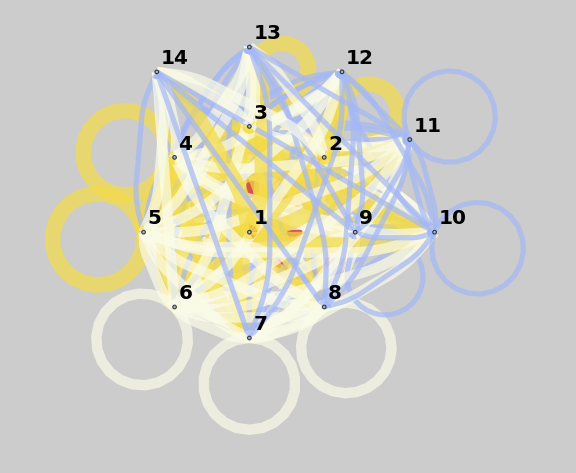

```mathematica
draw[predictedList]
```

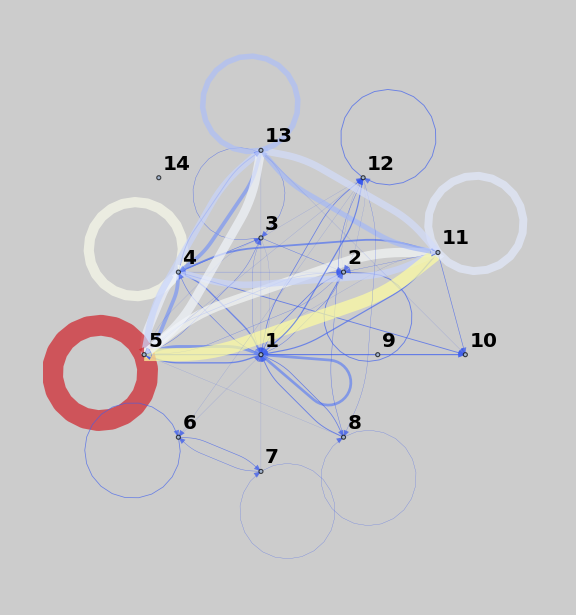

```mathematica
draw[realData]
```

```mathematica
outData=Table[
out=Table[
If[d[[1]]==i&&d[[2]]==j,
d
,
Nothing[]
]
,{d,mainDataList5}]
,{i,1,14},{j,1,14}];
```

```mathematica
Dimensions@outData
```

{14,14,5,4}

```mathematica
outData[[1,1]]
```

{{1,1,2015,9},{1,1,2016,13},{1,1,2017,14},{1,1,2018,16},{1,1,2019,18}}

```mathematica
linOut=Table[

LinearModelFit[outData[[i,j]][[All,3;;-1]],{x1},{x1}]

,{i,1,14},{j,14}];
```

```mathematica
linOut
```

{{FittedModel[-4221.7+2.1 x1],FittedModel[-1407.9+0.7 x1],FittedModel[2.-1.08508×10^-16 x1],FittedModel[4.-2.17016×10^-16 x1],FittedModel[-1809.7+0.9 x1],FittedModel[0.],FittedModel[0.],FittedModel[-1004.1+0.5 x1],FittedModel[0.],FittedModel[3.-1.62663×10^-16 x1],FittedModel[0.],FittedModel[-2215.3+1.1 x1],FittedModel[0.],FittedModel[0.]},{FittedModel[-1410.5+0.7 x1],FittedModel[-1811.7+0.9 x1],FittedModel[0.],FittedModel[-1007.9+0.5 x1],FittedModel[-1007.9+0.5 x1],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[-604.7+0.3 x1],FittedModel[0.],FittedModel[0.]},{FittedModel[-604.7+0.3 x1],FittedModel[-1208.2+0.6 x1],FittedModel[-1006.1+0.5 x1],FittedModel[-1408.7+0.7 x1],FittedModel[-1006.1+0.5 x1],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[-604.7+0.3 x1],FittedModel[0.],FittedModel[0.]},{FittedModel[-2211.5+1.1 x1],FittedModel[0.],FittedModel[0.],FittedModel[-12481.8+6.2 x1],FittedModel[-10070.4+5. x1],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[-1608.8+0.8 x1],FittedModel[-6450.+3.2 x1],FittedModel[-403.2+0.2 x1],FittedModel[-3023.7+1.5 x1],FittedModel[0.]},{FittedModel[-4224.1+2.1 x1],FittedModel[-1812.3+0.9 x1],FittedModel[-402.6+0.2 x1],FittedModel[-23157.5+11.5 x1],FittedModel[-52368.8+26. x1],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[-2011.4+1. x1],FittedModel[-28419.5+14.1 x1],FittedModel[0.],FittedModel[-16529.4+8.2 x1],FittedModel[0.]},{FittedModel[1.-5.42539×10^-17 x1],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[-1407.7+0.7 x1],FittedModel[-601.5+0.3 x1],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.]},{FittedModel[1.-5.42539×10^-17 x1],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[-1409.7+0.7 x1],FittedModel[-603.5+0.3 x1],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.]},{FittedModel[-2416.6+1.2 x1],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[-403.2+0.2 x1],FittedModel[0.],FittedModel[0.],FittedModel[-1007.1+0.5 x1],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[-1006.1+0.5 x1],FittedModel[0.],FittedModel[0.]},{FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.]},{FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.]},{FittedModel[-2619.1+1.3 x1],FittedModel[-1007.1+0.5 x1],FittedModel[0.],FittedModel[-20753.1+10.3 x1],FittedModel[-39292.3+19.5 x1],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[-2418.2+1.2 x1],FittedModel[-23175.1+11.5 x1],FittedModel[0.],FittedModel[-14715.1+7.3 x1],FittedModel[0.]},{FittedModel[-2619.7+1.3 x1],FittedModel[-604.7+0.3 x1],FittedModel[0.],FittedModel[0.],FittedModel[-403.2+0.2 x1],FittedModel[-604.7+0.3 x1],FittedModel[0.],FittedModel[-1007.1+0.5 x1],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[-2819.8+1.4 x1],FittedModel[0.],FittedModel[0.]},{FittedModel[-604.5+0.3 x1],FittedModel[0.],FittedModel[0.],FittedModel[-11891.3+5.9 x1],FittedModel[-27008.+13.4 x1],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[-604.5+0.3 x1],FittedModel[-22373.3+11.1 x1],FittedModel[0.],FittedModel[-14715.1+7.3 x1],FittedModel[0.]},{FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.],FittedModel[0.]}}

```mathematica
predictedList2={};
```

```mathematica
For[i=1,i<=14,i++,
tempSubList={};
For[j=1,j<=14,j++,
tempOuput=Abs@Floor@linOut[[i]][[j]][j];
AppendTo[tempSubList, Floor[tempOuput]];
];
AppendTo[predictedList2,tempSubList];
];
```

```mathematica
predictedList2
```

{{4220,1407,2,4,1806,0,0,1001,0,3,0,2203,0,0},{1410,1810,0,1006,1006,0,0,0,0,0,0,602,0,0},{605,1208,1005,1406,1004,0,0,0,0,0,0,602,0,0},{2211,0,0,12458,10046,0,0,0,0,1601,6415,401,3005,0},{4223,1811,403,23112,52239,0,0,0,0,2002,28265,0,16423,0},{1,0,0,0,0,1404,600,0,0,0,0,0,0,0},{1,0,0,0,0,1406,602,0,0,0,0,0,0,0},{2416,0,0,0,403,0,0,1004,0,0,0,1001,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2618,1007,0,20712,39195,0,0,0,0,2407,23049,0,14621,0},{2619,605,0,0,403,603,0,1004,0,0,0,2804,0,0},{605,0,0,11868,26942,0,0,0,0,602,22252,0,14621,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
pts[predictedList2, realData]
```

997.259

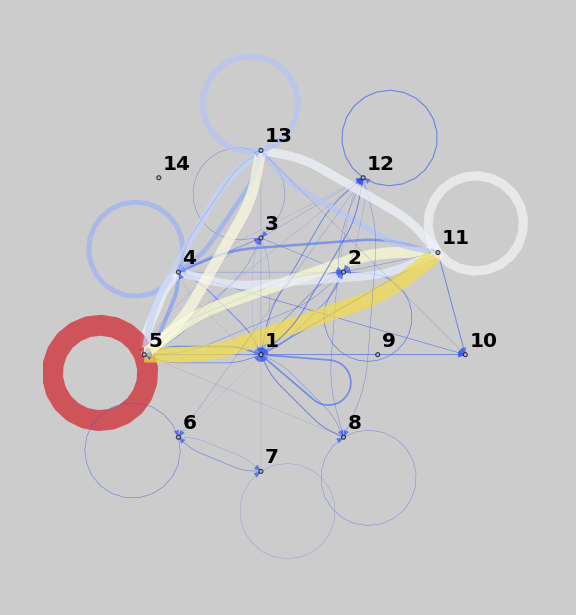

```mathematica
draw@predictedList2
```